```mathematica
Quit[]
```

```mathematica
NotebookDirectory[]
```

/home/riccardo/Documents/Fisica/Tesi/maindir/qqmm1L_massless_xi/qqmm1L_xi_A/reduction/

# Integral families cross reduction

## Input

```mathematica
<<"/home/riccardo/Programs/ABISS/ABISS/ABISS.m";
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

```mathematica
SetPath[NotebookDirectory[]];
process={F[3,{1,o}],-F[3,{1,o}]}->{F[2,{2}],-F[2,{2}]};
SetProcess[process];
```

```mathematica
GenerateInput[];
```

ABISS Warning: Input file /home/riccardo/Documents/Fisica/Tesi/maindir/qqmm1L_massless_xi/qqmm1L_xi_A/reduction/input/kinematics.m already exist. It will NOT be overwritten.

ABISS Warning: Input file /home/riccardo/Documents/Fisica/Tesi/maindir/qqmm1L_massless_xi/qqmm1L_xi_A/reduction/input/integral_families.m already exist. It will NOT be overwritten.

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/maindir/qqmm1L_massless_xi/qqmm1L_xi_A/reduction/input/kinematics.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/maindir/qqmm1L_massless_xi/qqmm1L_xi_A/reduction/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/maindir/qqmm1L_massless_xi/qqmm1L_xi_A/reduction/input/equivalence_classes.m

## Backup

```mathematica
fieldsBorn=<<(NotebookDirectory[]<>"backup/fields/fieldsBorn.m");
fields1L=<<(NotebookDirectory[]<>"backup/fields/fields1L.m");
```

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebf/cgdg/ghefehfh.m, 0 diagrams

> Top. 3 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 4 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 5 aebe/cfdf/egfggg.m, 0 diagrams

> Top. 6 aebe/cfdf/egfhghgh.m, 0 diagrams

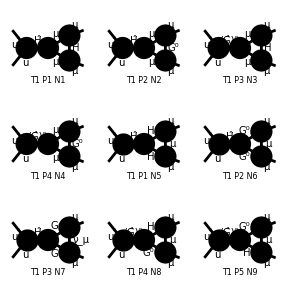

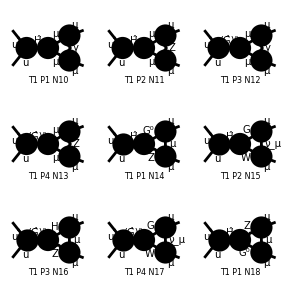

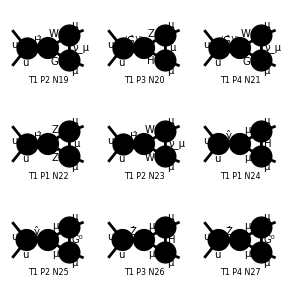

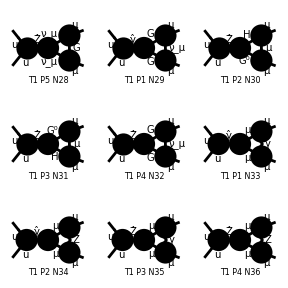

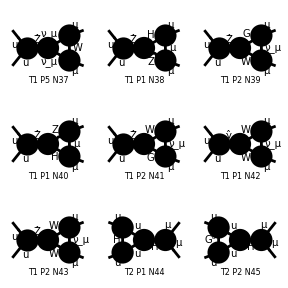

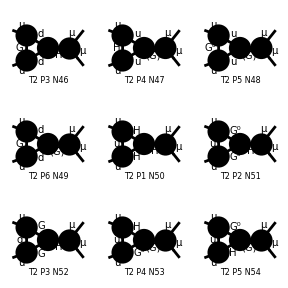

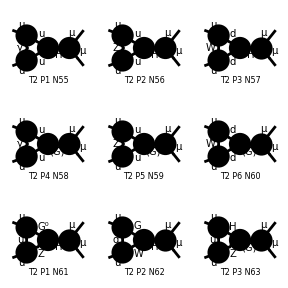

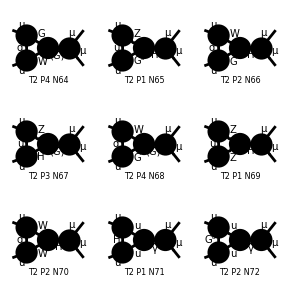

```mathematica
Paint [fields1L];
```

## Results

## Coefficients

#### Normal

```mathematica
imax=376;
jmax=1;
diagramCoefficients={};
timeCoefficients={};
Do[
diagramCoefficients=Append[diagramCoefficients,{}];
timeCoefficients=Append[timeCoefficients,{}];
,{j,jmax}];
Do[
Do[
Print[i," - ",j];
tmp1=AbsoluteTiming[Simplify[<<(NotebookDirectory[]<>"coefficients/Coefficients_"<>ToString[i]<>"_"<>ToString[j]<>".m")]];
diagramCoefficients[[j]]=Append[diagramCoefficients[[j]],tmp1[[2]]];
timeCoefficients[[j]]=Append[timeCoefficients[[j]],tmp1[[1]]]
,{i,1,imax}]
,{j,jmax}]
```

1 - 1

2 - 1

3 - 1

4 - 1

5 - 1

6 - 1

7 - 1

8 - 1

9 - 1

10 - 1

11 - 1

12 - 1

13 - 1

14 - 1

15 - 1

16 - 1

17 - 1

18 - 1

19 - 1

20 - 1

21 - 1

22 - 1

23 - 1

24 - 1

25 - 1

26 - 1

27 - 1

28 - 1

29 - 1

30 - 1

31 - 1

32 - 1

33 - 1

34 - 1

35 - 1

36 - 1

37 - 1

38 - 1

39 - 1

40 - 1

41 - 1

42 - 1

43 - 1

44 - 1

45 - 1

46 - 1

47 - 1

48 - 1

49 - 1

50 - 1

51 - 1

52 - 1

53 - 1

54 - 1

55 - 1

56 - 1

57 - 1

58 - 1

59 - 1

60 - 1

61 - 1

62 - 1

63 - 1

64 - 1

65 - 1

66 - 1

67 - 1

68 - 1

69 - 1

70 - 1

71 - 1

72 - 1

73 - 1

74 - 1

75 - 1

76 - 1

77 - 1

78 - 1

79 - 1

80 - 1

81 - 1

82 - 1

83 - 1

84 - 1

85 - 1

86 - 1

87 - 1

88 - 1

89 - 1

90 - 1

91 - 1

92 - 1

93 - 1

94 - 1

95 - 1

96 - 1

97 - 1

98 - 1

99 - 1

100 - 1

101 - 1

102 - 1

103 - 1

104 - 1

105 - 1

106 - 1

107 - 1

108 - 1

109 - 1

110 - 1

111 - 1

112 - 1

113 - 1

114 - 1

115 - 1

116 - 1

117 - 1

118 - 1

119 - 1

120 - 1

121 - 1

122 - 1

123 - 1

124 - 1

125 - 1

126 - 1

127 - 1

128 - 1

129 - 1

130 - 1

131 - 1

132 - 1

133 - 1

134 - 1

135 - 1

136 - 1

137 - 1

138 - 1

139 - 1

140 - 1

141 - 1

142 - 1

143 - 1

144 - 1

145 - 1

146 - 1

147 - 1

148 - 1

149 - 1

150 - 1

151 - 1

152 - 1

153 - 1

154 - 1

155 - 1

156 - 1

157 - 1

158 - 1

159 - 1

160 - 1

161 - 1

162 - 1

163 - 1

164 - 1

165 - 1

166 - 1

167 - 1

168 - 1

169 - 1

170 - 1

171 - 1

172 - 1

173 - 1

174 - 1

175 - 1

176 - 1

177 - 1

178 - 1

179 - 1

180 - 1

181 - 1

182 - 1

183 - 1

184 - 1

185 - 1

186 - 1

187 - 1

188 - 1

189 - 1

190 - 1

191 - 1

192 - 1

193 - 1

194 - 1

195 - 1

196 - 1

197 - 1

198 - 1

199 - 1

200 - 1

201 - 1

202 - 1

203 - 1

204 - 1

205 - 1

206 - 1

207 - 1

208 - 1

209 - 1

210 - 1

211 - 1

212 - 1

213 - 1

214 - 1

215 - 1

216 - 1

217 - 1

218 - 1

219 - 1

220 - 1

221 - 1

222 - 1

223 - 1

224 - 1

225 - 1

226 - 1

227 - 1

228 - 1

229 - 1

230 - 1

231 - 1

232 - 1

233 - 1

234 - 1

235 - 1

236 - 1

237 - 1

238 - 1

239 - 1

240 - 1

241 - 1

242 - 1

243 - 1

244 - 1

245 - 1

246 - 1

247 - 1

248 - 1

249 - 1

250 - 1

251 - 1

252 - 1

253 - 1

254 - 1

255 - 1

256 - 1

257 - 1

258 - 1

259 - 1

260 - 1

261 - 1

262 - 1

263 - 1

264 - 1

265 - 1

266 - 1

267 - 1

268 - 1

269 - 1

270 - 1

271 - 1

272 - 1

273 - 1

274 - 1

275 - 1

276 - 1

277 - 1

278 - 1

279 - 1

280 - 1

281 - 1

282 - 1

283 - 1

284 - 1

285 - 1

286 - 1

287 - 1

288 - 1

289 - 1

290 - 1

291 - 1

292 - 1

293 - 1

294 - 1

295 - 1

296 - 1

297 - 1

298 - 1

299 - 1

300 - 1

301 - 1

302 - 1

303 - 1

304 - 1

305 - 1

306 - 1

307 - 1

308 - 1

309 - 1

310 - 1

311 - 1

312 - 1

313 - 1

314 - 1

315 - 1

316 - 1

317 - 1

318 - 1

319 - 1

320 - 1

321 - 1

322 - 1

323 - 1

324 - 1

325 - 1

326 - 1

327 - 1

328 - 1

329 - 1

330 - 1

331 - 1

332 - 1

333 - 1

334 - 1

335 - 1

336 - 1

337 - 1

338 - 1

339 - 1

340 - 1

341 - 1

342 - 1

343 - 1

344 - 1

345 - 1

346 - 1

347 - 1

348 - 1

349 - 1

350 - 1

351 - 1

352 - 1

353 - 1

354 - 1

355 - 1

356 - 1

357 - 1

358 - 1

359 - 1

360 - 1

361 - 1

362 - 1

363 - 1

364 - 1

365 - 1

366 - 1

367 - 1

368 - 1

369 - 1

370 - 1

371 - 1

372 - 1

373 - 1

374 - 1

375 - 1

376 - 1

#### Replace

```mathematica
imax=376;
jmax=1;
diagramCoefficientsRep={};
timeCoefficientsRep={};
Do[
diagramCoefficientsRep=Append[diagramCoefficientsRep,{}];
timeCoefficientsRep=Append[timeCoefficientsRep,{}];
,{j,jmax}];
Do[
Do[
Print[i," - ",j];
tmp1=AbsoluteTiming[Simplify[(<<(NotebookDirectory[]<>"coefficients/Coefficients_"<>ToString[i]<>"_"<>ToString[j]<>".m"))/.parameterReplace/.cwReplace]];
diagramCoefficientsRep[[j]]=Append[diagramCoefficientsRep[[j]],tmp1[[2]]];
timeCoefficientsRep[[j]]=Append[timeCoefficientsRep[[j]],tmp1[[1]]]
,{i,1,imax}]
,{j,jmax}]
```

1 - 1

2 - 1

3 - 1

4 - 1

5 - 1

6 - 1

7 - 1

8 - 1

9 - 1

10 - 1

11 - 1

12 - 1

13 - 1

14 - 1

15 - 1

16 - 1

17 - 1

18 - 1

19 - 1

20 - 1

21 - 1

22 - 1

23 - 1

24 - 1

25 - 1

26 - 1

27 - 1

28 - 1

29 - 1

30 - 1

31 - 1

32 - 1

33 - 1

34 - 1

35 - 1

36 - 1

37 - 1

38 - 1

39 - 1

40 - 1

41 - 1

42 - 1

43 - 1

44 - 1

45 - 1

46 - 1

47 - 1

48 - 1

49 - 1

50 - 1

51 - 1

52 - 1

53 - 1

54 - 1

55 - 1

56 - 1

57 - 1

58 - 1

59 - 1

60 - 1

61 - 1

62 - 1

63 - 1

64 - 1

65 - 1

66 - 1

67 - 1

68 - 1

69 - 1

70 - 1

71 - 1

72 - 1

73 - 1

74 - 1

75 - 1

76 - 1

77 - 1

78 - 1

79 - 1

80 - 1

81 - 1

82 - 1

83 - 1

84 - 1

85 - 1

86 - 1

87 - 1

88 - 1

89 - 1

90 - 1

91 - 1

92 - 1

93 - 1

94 - 1

95 - 1

96 - 1

97 - 1

98 - 1

99 - 1

100 - 1

101 - 1

102 - 1

103 - 1

104 - 1

105 - 1

106 - 1

107 - 1

108 - 1

109 - 1

110 - 1

111 - 1

112 - 1

113 - 1

114 - 1

115 - 1

116 - 1

117 - 1

118 - 1

119 - 1

120 - 1

121 - 1

122 - 1

123 - 1

124 - 1

125 - 1

126 - 1

127 - 1

128 - 1

129 - 1

130 - 1

131 - 1

132 - 1

133 - 1

134 - 1

135 - 1

136 - 1

137 - 1

138 - 1

139 - 1

140 - 1

141 - 1

142 - 1

143 - 1

144 - 1

145 - 1

146 - 1

147 - 1

148 - 1

149 - 1

150 - 1

151 - 1

152 - 1

153 - 1

154 - 1

155 - 1

156 - 1

157 - 1

158 - 1

159 - 1

160 - 1

161 - 1

162 - 1

163 - 1

164 - 1

165 - 1

166 - 1

167 - 1

168 - 1

169 - 1

170 - 1

171 - 1

172 - 1

173 - 1

174 - 1

175 - 1

176 - 1

177 - 1

178 - 1

179 - 1

180 - 1

181 - 1

182 - 1

183 - 1

184 - 1

185 - 1

186 - 1

187 - 1

188 - 1

189 - 1

190 - 1

191 - 1

192 - 1

193 - 1

194 - 1

195 - 1

196 - 1

197 - 1

198 - 1

199 - 1

200 - 1

201 - 1

202 - 1

203 - 1

204 - 1

205 - 1

206 - 1

207 - 1

208 - 1

209 - 1

210 - 1

211 - 1

212 - 1

213 - 1

214 - 1

215 - 1

216 - 1

217 - 1

218 - 1

219 - 1

220 - 1

221 - 1

222 - 1

223 - 1

224 - 1

225 - 1

226 - 1

227 - 1

228 - 1

229 - 1

230 - 1

231 - 1

232 - 1

233 - 1

234 - 1

235 - 1

236 - 1

237 - 1

238 - 1

239 - 1

240 - 1

241 - 1

242 - 1

243 - 1

244 - 1

245 - 1

246 - 1

247 - 1

248 - 1

249 - 1

250 - 1

251 - 1

252 - 1

253 - 1

254 - 1

255 - 1

256 - 1

257 - 1

258 - 1

259 - 1

260 - 1

261 - 1

262 - 1

263 - 1

264 - 1

265 - 1

266 - 1

267 - 1

268 - 1

269 - 1

270 - 1

271 - 1

272 - 1

273 - 1

274 - 1

275 - 1

276 - 1

277 - 1

278 - 1

279 - 1

280 - 1

281 - 1

282 - 1

283 - 1

284 - 1

285 - 1

286 - 1

287 - 1

288 - 1

289 - 1

290 - 1

291 - 1

292 - 1

293 - 1

294 - 1

295 - 1

296 - 1

297 - 1

298 - 1

299 - 1

300 - 1

301 - 1

302 - 1

303 - 1

304 - 1

305 - 1

306 - 1

307 - 1

308 - 1

309 - 1

310 - 1

311 - 1

312 - 1

313 - 1

314 - 1

315 - 1

316 - 1

317 - 1

318 - 1

319 - 1

320 - 1

321 - 1

322 - 1

323 - 1

324 - 1

325 - 1

326 - 1

327 - 1

328 - 1

329 - 1

330 - 1

331 - 1

332 - 1

333 - 1

334 - 1

335 - 1

336 - 1

337 - 1

338 - 1

339 - 1

340 - 1

341 - 1

342 - 1

343 - 1

344 - 1

345 - 1

346 - 1

347 - 1

348 - 1

349 - 1

350 - 1

351 - 1

352 - 1

353 - 1

354 - 1

355 - 1

356 - 1

357 - 1

358 - 1

359 - 1

360 - 1

361 - 1

362 - 1

363 - 1

364 - 1

365 - 1

366 - 1

367 - 1

368 - 1

369 - 1

370 - 1

371 - 1

372 - 1

373 - 1

374 - 1

375 - 1

376 - 1

## Backup

#### Save

```mathematica
diagramCoefficients>>(NotebookDirectory[]<>"final_results/diagramCoefficients.m");
diagramCoefficientsRep>>(NotebookDirectory[]<>"final_results/diagramCoefficientsRep.m");
timeCoefficients>>(NotebookDirectory[]<>"final_results/diagramTime.m");
```

#### Load

```mathematica
diagramCoefficients=<<(NotebookDirectory[]<>"final_results/diagramCoefficients.m");
diagramCoefficientsRep=<<(NotebookDirectory[]<>"final_results/diagramCoefficientsRep.m");
timeCoefficients=<<(NotebookDirectory[]<>"final_results/diagramTime.m");
masters=<<(NotebookDirectory[]<>"coefficients/Masters.m");
(*Print["Number of masters: ",Length[masters]];
Print["Number of diagrams: ",Length[diagramCoefficients[[1]]]];*)
```

### Masters

```mathematica
masters=<<(NotebookDirectory[]<>"coefficients/Masters.m");
```

```mathematica
Print["Total masters  r: ",findR[masters]," s: ",findS[masters]]
```

Total masters  r: 4 s: 0

```mathematica
Do[
sitmp=collectByIFname[masters,userIntegralFamiliesNames[[i]]];
rtmp=findR[sitmp];
stmp=findS[sitmp];
Print[ToString[userIntegralFamiliesNames[[i]]],"  r: ",rtmp," s: ",stmp," sectors: ",findActiveSectors[sitmp],"  ", userIntegralMasses[userIntegralFamiliesNames[[i]]]]
,{i,Length[userIntegralFamiliesNames]}]
```

A01  r: 4 s: 0 sectors: {1,1,1,1,0,0,0,0,0}  {0,0,0,0}

B01  r: 4 s: 0 sectors: {1,1,1,1,0,0,0,0,0}  {0,0,0,0}

A11  r: 4 s: 0 sectors: {1,1,1,1,0,0,0,0,0}  {0,0,M1,0}

A12  r: 3 s: 0 sectors: {0,1,1,1,0,0,0,0,0}  {0,0,0,M1}

B11  r: 4 s: 0 sectors: {1,1,1,1,0,0,0,0,0}  {0,0,M1,0}

A21  r: 4 s: 0 sectors: {1,1,1,1,0,0,0,0,0}  {0,M1,M1,0}

A22  r: 3 s: 0 sectors: {0,1,1,1,0,0,0,0,0}  {0,M1,M2,0}

B21  r: 4 s: 0 sectors: {1,1,1,1,0,0,0,0,0}  {0,M1,M1,0}

B22  r: 4 s: 0 sectors: {1,1,1,1,0,0,0,0,0}  {0,M1,M2,0}

## Rules

```mathematica
kirarules=<<(NotebookDirectory[]<>"rules/kira_myintegrals.m");
```

```mathematica
kirarules
```

{A11p1[1,0,0,1]→A01p1[1,0,0,1],A21p1[0,1,0,0]→A11p1[0,0,1,0],A21p1[0,1,0,0]→A11p1[0,0,1,0],A21p1[1,0,0,1]→A01p1[1,0,0,1],A21p1[1,1,0,1]→A11p1[1,0,1,1],A22p2[0,0,1,0]→A11p1[0,0,1,0],A22p1[0,1,0,0]→A11p1[0,0,1,0],A22p2[0,1,0,0]→A22p1[0,0,1,0],A22p2[0,1,1,0]→A22p1[0,1,1,0],B01p1[0,1,1,0]→A01p1[0,1,1,0],B11p1[0,0,1,0]→A11p1[0,0,1,0],B11p1[0,1,1,0]→A11p1[0,1,1,0],B11p1[1,0,0,1]→B01p1[1,0,0,1],B11p1[0,1,1,0]→A11p1[0,1,1,0],B11p1[0,0,1,0]→A11p1[0,0,1,0],B22p1[0,0,1,0]→A22p1[0,0,1,0],B22p2[0,0,1,0]→A11p1[0,0,1,0],B22p1[0,1,0,0]→A11p1[0,0,1,0],B22p2[0,1,0,0]→A22p1[0,0,1,0],B22p1[0,1,1,0]→A22p1[0,1,1,0],B22p2[0,1,1,0]→A22p1[0,1,1,0],B22p2[1,1,1,1]→B22p1[1,1,1,1],B21p1[0,1,0,0]→A11p1[0,0,1,0],B21p1[0,1,1,0]→A21p1[0,1,1,0],B21p1[0,1,0,0]→A11p1[0,0,1,0],B21p1[0,1,1,0]→A21p1[0,1,1,0],B21p1[1,1,1,0]→A21p1[1,1,1,0],B21p1[1,0,0,1]→B01p1[1,0,0,1],B21p1[1,1,0,1]→B11p1[1,0,1,1],B22p1[0,0,1,0]→A22p1[0,0,1,0],B22p2[0,0,1,0]→A11p1[0,0,1,0],B22p1[0,1,0,0]→A11p1[0,0,1,0],B22p2[0,1,0,0]→A22p1[0,0,1,0],B22p1[0,1,1,0]→A22p1[0,1,1,0],B22p2[0,1,1,0]→A22p1[0,1,1,0],B21p1[0,1,0,0]→A11p1[0,0,1,0],B21p1[0,1,1,0]→A21p1[0,1,1,0],B21p1[0,1,0,0]→A11p1[0,0,1,0],B21p1[0,1,1,0]→A21p1[0,1,1,0],B21p1[1,1,1,0]→A21p1[1,1,1,0],B21p1[1,0,0,1]→B01p1[1,0,0,1],B21p1[1,1,0,1]→B11p1[1,0,1,1],A12p1[0,0,0,1]→A11p1[0,0,1,0],A12p1[0,1,1,0]→A01p1[0,1,1,0],A12p1[0,0,0,1]→A11p1[0,0,1,0],A12p1[0,0,0,1]→A11p1[0,0,1,0],A12p1[0,0,0,1]→A11p1[0,0,1,0],A12p1[0,1,1,0]→A01p1[0,1,1,0],A22p2[0,0,1,0]→A11p1[0,0,1,0],A22p1[0,1,0,0]→A11p1[0,0,1,0],A22p2[0,1,0,0]→A22p1[0,0,1,0],A22p2[0,1,1,0]→A22p1[0,1,1,0],A21p1[0,1,0,0]→A11p1[0,0,1,0],A21p1[0,1,0,0]→A11p1[0,0,1,0],A22p2[0,1,1,1]→A22p1[0,1,1,1],A21p1[0,1,0,0]→A11p1[0,0,1,0],A21p1[0,1,0,0]→A11p1[0,0,1,0],A22p2[0,0,1,0]→A11p1[0,0,1,0],A22p1[0,1,0,0]→A11p1[0,0,1,0],A22p2[0,1,0,0]→A22p1[0,0,1,0],A22p2[0,1,1,0]→A22p1[0,1,1,0],A22p2[0,0,1,0]→A11p1[0,0,1,0],A22p1[0,1,0,0]→A11p1[0,0,1,0],A22p2[0,1,0,0]→A22p1[0,0,1,0],A22p2[0,1,1,0]→A22p1[0,1,1,0]}

```mathematica
rules=ruleTransform[kirarules];
rules=deleteDoubleRules[rules];
rules=deletePermutations[rules];
```

```mathematica
diagramCoefficients//Variables
```

{d,EL,gAd,gAl,gAu,gFFA,gFFAA,gFFAZ,gFFZ,gFFZZ,gFZW,ggmgmA,ggmgmAA,ggmgmAZ,ggmgmZ,ggmgmZZ,ggpgpA,ggpgpAA,ggpgpAZ,ggpgpZ,ggpgpZZ,gHHZZ,gHXZ,gHZZ,gWdu,gWlN,gWNl,gWud,gWWA,gWWAA,gWWAZ,gWWZ,gWWZZ,gXXZZ,gZdL,gZlL,gZlR,gZNL,gZuL,gZuR,mh,ml,mw,mz,s,sw,t,μ,μ^d,CKM[1,1],CKMC[1,1],GaugeXi[Q]}

```mathematica
rules
```

{userIntegral[A11,{m1_},1,0,0,1]→userIntegral[A01,{0},1,0,0,1],userIntegral[A21,{m1_},0,1,0,0]→userIntegral[A11,{m1},0,0,1,0],userIntegral[A21,{m1_},1,0,0,1]→userIntegral[A01,{0},1,0,0,1],userIntegral[A21,{m1_},1,1,0,1]→userIntegral[A11,{m1},1,0,1,1],userIntegral[A22,{m1_,m2_},0,0,1,0]→userIntegral[A11,{m2},0,0,1,0],userIntegral[A22,{m1_,m2_},0,1,0,0]→userIntegral[A11,{m1},0,0,1,0],userIntegral[B01,{0},0,1,1,0]→userIntegral[A01,{0},0,1,1,0],userIntegral[B11,{m1_},0,0,1,0]→userIntegral[A11,{m1},0,0,1,0],userIntegral[B11,{m1_},0,1,1,0]→userIntegral[A11,{m1},0,1,1,0],userIntegral[B11,{m1_},1,0,0,1]→userIntegral[B01,{0},1,0,0,1],userIntegral[B22,{m1_,m2_},0,0,1,0]→userIntegral[A22,{m1,m2},0,0,1,0],userIntegral[B22,{m1_,m2_},0,1,0,0]→userIntegral[A11,{m1},0,0,1,0],userIntegral[B22,{m1_,m2_},0,1,1,0]→userIntegral[A22,{m1,m2},0,1,1,0],userIntegral[B21,{m1_},0,1,0,0]→userIntegral[A11,{m1},0,0,1,0],userIntegral[B21,{m1_},0,1,1,0]→userIntegral[A21,{m1},0,1,1,0],userIntegral[B21,{m1_},1,1,1,0]→userIntegral[A21,{m1},1,1,1,0],userIntegral[B21,{m1_},1,0,0,1]→userIntegral[B01,{0},1,0,0,1],userIntegral[B21,{m1_},1,1,0,1]→userIntegral[B11,{m1},1,0,1,1],userIntegral[A12,{m1_},0,0,0,1]→userIntegral[A11,{m1},0,0,1,0],userIntegral[A12,{m1_},0,1,1,0]→userIntegral[A01,{0},0,1,1,0]}

#### Random

```mathematica
uselessRule[rule_Rule]:=Module[{result},
result=False;
r1=rule[[1]];
r2=rule[[2]];
x1=r1/.userIntegral[_,_,x__]->{x};
x2=r2/.userIntegral[_,_,x__]->{x};
If[!FreeQ[Permutations[x1],x2],
result=MatchQ[r2,userIntegral[_,_,x1]]
]
]
```

```mathematica
rules[[-1]]//uselessRule
```

False

```mathematica
rules[[-3]]//uselessRule
```

False

```mathematica
rules[[-3]]
```

userIntegral[F3,{m1_,m2_,m3_},0,2,0,1,1,0,0,0,0]→userIntegral[F3,{m3,m2,m1},0,1,0,2,1,0,0,0,0]

```mathematica
Permutations[]
```

```mathematica
Cases[rules/.Rule->List,{userIntegral[n_,___],userIntegral[n_,___]},1]
```

{{userIntegral[D6,{m1_,m2_},0,1,1,0,0,0,0,0,0],userIntegral[D6,{m2,m1},0,1,1,0,0,0,0,0,0]},{userIntegral[D6,{m1_,m2_},0,1,1,0,1,0,0,0,0],userIntegral[D6,{m2,m1},0,1,1,0,1,0,0,0,0]},{userIntegral[D6,{m1_,m2_},1,1,0,0,1,0,0,0,0],userIntegral[D6,{m2,m1},0,0,1,1,1,0,0,0,0]},{userIntegral[B12,{m1_,m2_},0,1,1,1,0,1,0,0,0],userIntegral[B12,{m2,m1},0,1,1,1,0,1,0,0,0]},{userIntegral[F2,{m1_,m2_},0,1,0,1,1,0,0,0,0],userIntegral[F2,{m2,m1},0,1,0,1,1,0,0,0,0]},{userIntegral[F2,{m1_,m2_},0,1,0,1,2,0,0,0,0],userIntegral[F2,{m2,m1},0,1,0,2,1,0,0,0,0]},{userIntegral[F2,{m1_,m2_},0,1,0,2,1,0,0,0,0],userIntegral[F2,{m2,m1},0,1,0,1,2,0,0,0,0]},{userIntegral[H1,{m1_,m2_},1,1,0,1,1,0,0,0,0],userIntegral[H1,{m2,m1},1,1,0,1,1,0,0,0,0]},{userIntegral[H1,{m1_,m2_},1,1,0,1,2,0,0,0,0],userIntegral[H1,{m2,m1},1,1,0,1,2,0,0,0,0]},{userIntegral[H1,{m1_,m2_},1,1,0,2,1,0,0,0,0],userIntegral[H1,{m2,m1},1,2,0,1,1,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,0,1,1,0,0,0,0,0],userIntegral[F3,{m1,m3,m2},0,0,1,1,0,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,0,1,1,0,0,0,0],userIntegral[F3,{m1,m3,m2},0,1,0,1,1,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,0,1,2,0,0,0,0],userIntegral[F3,{m1,m3,m2},0,1,0,2,1,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,0,2,1,0,0,0,0],userIntegral[F3,{m1,m3,m2},0,1,0,1,2,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,1,0,0,0,0,0,0],userIntegral[F3,{m1,m3,m2},0,1,0,1,0,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,1,1,0,0,0,0,0],userIntegral[F3,{m1,m3,m2},0,1,1,1,0,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,2,0,1,1,0,0,0,0],userIntegral[F3,{m1,m3,m2},0,2,0,1,1,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,0,1,1,0,0,0,0,0],userIntegral[F3,{m3,m1,m2},0,1,0,1,0,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,0,1,1,1,0,0,0,0],userIntegral[F3,{m3,m2,m1},0,1,1,0,1,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,0,1,1,0,0,0,0],userIntegral[F3,{m3,m1,m2},0,1,0,1,1,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,0,1,2,0,0,0,0],userIntegral[F3,{m3,m1,m2},0,1,0,2,1,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,0,2,1,0,0,0,0],userIntegral[F3,{m3,m1,m2},0,2,0,1,1,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,1,0,0,0,0,0,0],userIntegral[F3,{m3,m1,m2},0,0,1,1,0,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,1,0,1,0,0,0,0],userIntegral[F3,{m3,m2,m1},0,0,1,1,1,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,1,1,0,0,0,0,0],userIntegral[F3,{m3,m1,m2},0,1,1,1,0,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,1,1,1,0,0,0,0],userIntegral[F3,{m3,m2,m1},0,1,1,1,1,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,2,0,1,1,0,0,0,0],userIntegral[F3,{m3,m1,m2},0,1,0,1,2,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},1,0,1,1,1,0,0,0,0],userIntegral[F3,{m3,m2,m1},1,1,1,0,1,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},1,1,0,1,1,0,0,0,0],userIntegral[F3,{m3,m2,m1},1,1,0,1,1,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},1,1,1,0,1,0,0,0,0],userIntegral[F3,{m3,m2,m1},1,0,1,1,1,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},1,1,1,1,1,0,0,0,0],userIntegral[F3,{m3,m2,m1},1,1,1,1,1,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,0,1,1,0,0,0,0,0],userIntegral[F3,{m2,m1,m3},0,1,0,1,0,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,0,1,0,0,0,0,0],userIntegral[F3,{m2,m1,m3},0,0,1,1,0,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,0,1,1,0,0,0,0],userIntegral[F3,{m2,m1,m3},0,1,0,1,1,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,0,1,2,0,0,0,0],userIntegral[F3,{m2,m1,m3},0,2,0,1,1,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,0,2,1,0,0,0,0],userIntegral[F3,{m2,m1,m3},0,1,0,2,1,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,1,1,0,0,0,0,0],userIntegral[F3,{m2,m1,m3},0,1,1,1,0,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,2,0,1,1,0,0,0,0],userIntegral[F3,{m2,m1,m3},0,1,0,1,2,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},1,1,0,1,0,0,0,0,0],userIntegral[F3,{m1,m3,m2},0,1,1,0,0,1,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,0,1,0,0,0,0,0],userIntegral[F3,{m2,m3,m1},0,0,1,1,0,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,0,1,1,0,0,0,0],userIntegral[F3,{m2,m3,m1},0,1,0,1,1,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,0,1,2,0,0,0,0],userIntegral[F3,{m2,m3,m1},0,2,0,1,1,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,0,2,1,0,0,0,0],userIntegral[F3,{m2,m3,m1},0,1,0,1,2,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,1,0,0,0,0,0,0],userIntegral[F3,{m2,m3,m1},0,1,0,1,0,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,1,1,0,0,0,0,0],userIntegral[F3,{m2,m3,m1},0,1,1,1,0,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,2,0,1,1,0,0,0,0],userIntegral[F3,{m2,m3,m1},0,1,0,2,1,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},1,1,0,1,0,0,0,0,0],userIntegral[F3,{m3,m1,m2},0,1,1,0,0,1,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,0,1,0,0,0,0,0],userIntegral[F3,{m3,m2,m1},0,1,0,1,0,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,0,1,1,0,0,0,0],userIntegral[F3,{m3,m2,m1},0,1,0,1,1,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,0,1,2,0,0,0,0],userIntegral[F3,{m3,m2,m1},0,1,0,1,2,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,0,2,1,0,0,0,0],userIntegral[F3,{m3,m2,m1},0,2,0,1,1,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,1,0,0,0,0,0,0],userIntegral[F3,{m3,m2,m1},0,0,1,1,0,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,1,1,1,0,0,0,0,0],userIntegral[F3,{m3,m2,m1},0,1,1,1,0,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},0,2,0,1,1,0,0,0,0],userIntegral[F3,{m3,m2,m1},0,1,0,2,1,0,0,0,0]},{userIntegral[F3,{m1_,m2_,m3_},1,1,0,1,0,0,0,0,0],userIntegral[F3,{m3,m2,m1},1,1,0,1,0,0,0,0,0]}}

## New Masters

```mathematica
imax=376;
jmax=1;
diagramTotal={};
Do[
diagramTotal=Append[diagramTotal,{}];
,{j,jmax}];
Do[
Do[
Print[i," - ",j];
tmptot=Plus@@(diagramCoefficients[[j,i]]*masters);
tmptot=tmptot//.rules;
diagramTotal[[j]]=Append[diagramTotal[[j]],tmptot]
,{i,1,imax}]
,{j,jmax}]
```

1 - 1

2 - 1

3 - 1

4 - 1

5 - 1

6 - 1

7 - 1

8 - 1

9 - 1

10 - 1

11 - 1

12 - 1

13 - 1

14 - 1

15 - 1

16 - 1

17 - 1

18 - 1

19 - 1

20 - 1

21 - 1

22 - 1

23 - 1

24 - 1

25 - 1

26 - 1

27 - 1

28 - 1

29 - 1

30 - 1

31 - 1

32 - 1

33 - 1

34 - 1

35 - 1

36 - 1

37 - 1

38 - 1

39 - 1

40 - 1

41 - 1

42 - 1

43 - 1

44 - 1

45 - 1

46 - 1

47 - 1

48 - 1

49 - 1

50 - 1

51 - 1

52 - 1

53 - 1

54 - 1

55 - 1

56 - 1

57 - 1

58 - 1

59 - 1

60 - 1

61 - 1

62 - 1

63 - 1

64 - 1

65 - 1

66 - 1

67 - 1

68 - 1

69 - 1

70 - 1

71 - 1

72 - 1

73 - 1

74 - 1

75 - 1

76 - 1

77 - 1

78 - 1

79 - 1

80 - 1

81 - 1

82 - 1

83 - 1

84 - 1

85 - 1

86 - 1

87 - 1

88 - 1

89 - 1

90 - 1

91 - 1

92 - 1

93 - 1

94 - 1

95 - 1

96 - 1

97 - 1

98 - 1

99 - 1

100 - 1

101 - 1

102 - 1

103 - 1

104 - 1

105 - 1

106 - 1

107 - 1

108 - 1

109 - 1

110 - 1

111 - 1

112 - 1

113 - 1

114 - 1

115 - 1

116 - 1

117 - 1

118 - 1

119 - 1

120 - 1

121 - 1

122 - 1

123 - 1

124 - 1

125 - 1

126 - 1

127 - 1

128 - 1

129 - 1

130 - 1

131 - 1

132 - 1

133 - 1

134 - 1

135 - 1

136 - 1

137 - 1

138 - 1

139 - 1

140 - 1

141 - 1

142 - 1

143 - 1

144 - 1

145 - 1

146 - 1

147 - 1

148 - 1

149 - 1

150 - 1

151 - 1

152 - 1

153 - 1

154 - 1

155 - 1

156 - 1

157 - 1

158 - 1

159 - 1

160 - 1

161 - 1

162 - 1

163 - 1

164 - 1

165 - 1

166 - 1

167 - 1

168 - 1

169 - 1

170 - 1

171 - 1

172 - 1

173 - 1

174 - 1

175 - 1

176 - 1

177 - 1

178 - 1

179 - 1

180 - 1

181 - 1

182 - 1

183 - 1

184 - 1

185 - 1

186 - 1

187 - 1

188 - 1

189 - 1

190 - 1

191 - 1

192 - 1

193 - 1

194 - 1

195 - 1

196 - 1

197 - 1

198 - 1

199 - 1

200 - 1

201 - 1

202 - 1

203 - 1

204 - 1

205 - 1

206 - 1

207 - 1

208 - 1

209 - 1

210 - 1

211 - 1

212 - 1

213 - 1

214 - 1

215 - 1

216 - 1

217 - 1

218 - 1

219 - 1

220 - 1

221 - 1

222 - 1

223 - 1

224 - 1

225 - 1

226 - 1

227 - 1

228 - 1

229 - 1

230 - 1

231 - 1

232 - 1

233 - 1

234 - 1

235 - 1

236 - 1

237 - 1

238 - 1

239 - 1

240 - 1

241 - 1

242 - 1

243 - 1

244 - 1

245 - 1

246 - 1

247 - 1

248 - 1

249 - 1

250 - 1

251 - 1

252 - 1

253 - 1

254 - 1

255 - 1

256 - 1

257 - 1

258 - 1

259 - 1

260 - 1

261 - 1

262 - 1

263 - 1

264 - 1

265 - 1

266 - 1

267 - 1

268 - 1

269 - 1

270 - 1

271 - 1

272 - 1

273 - 1

274 - 1

275 - 1

276 - 1

277 - 1

278 - 1

279 - 1

280 - 1

281 - 1

282 - 1

283 - 1

284 - 1

285 - 1

286 - 1

287 - 1

288 - 1

289 - 1

290 - 1

291 - 1

292 - 1

293 - 1

294 - 1

295 - 1

296 - 1

297 - 1

298 - 1

299 - 1

300 - 1

301 - 1

302 - 1

303 - 1

304 - 1

305 - 1

306 - 1

307 - 1

308 - 1

309 - 1

310 - 1

311 - 1

312 - 1

313 - 1

314 - 1

315 - 1

316 - 1

317 - 1

318 - 1

319 - 1

320 - 1

321 - 1

322 - 1

323 - 1

324 - 1

325 - 1

326 - 1

327 - 1

328 - 1

329 - 1

330 - 1

331 - 1

332 - 1

333 - 1

334 - 1

335 - 1

336 - 1

337 - 1

338 - 1

339 - 1

340 - 1

341 - 1

342 - 1

343 - 1

344 - 1

345 - 1

346 - 1

347 - 1

348 - 1

349 - 1

350 - 1

351 - 1

352 - 1

353 - 1

354 - 1

355 - 1

356 - 1

357 - 1

358 - 1

359 - 1

360 - 1

361 - 1

362 - 1

363 - 1

364 - 1

365 - 1

366 - 1

367 - 1

368 - 1

369 - 1

370 - 1

371 - 1

372 - 1

373 - 1

374 - 1

375 - 1

376 - 1

```mathematica
mastersNew=DeleteDuplicates[Cases[diagramTotal,userIntegral[___],Infinity]];
Length[mastersNew]
```

34

#### Normal

```mathematica
imax=376;
jmax=1;
diagramCoefficientsNew={};
Do[
diagramCoefficientsNew=Append[diagramCoefficientsNew,{}];
,{j,jmax}];
Do[
Do[
Print[i," - ",j];
tmp=findCoefficients[diagramTotal[[j,i]],mastersNew];
diagramCoefficientsNew[[j]]=Append[diagramCoefficientsNew[[j]],tmp]
,{i,1,imax}]
,{j,jmax}]
```

1 - 1

2 - 1

3 - 1

4 - 1

5 - 1

6 - 1

7 - 1

8 - 1

9 - 1

10 - 1

11 - 1

12 - 1

13 - 1

14 - 1

15 - 1

16 - 1

17 - 1

18 - 1

19 - 1

20 - 1

21 - 1

22 - 1

23 - 1

24 - 1

25 - 1

26 - 1

27 - 1

28 - 1

29 - 1

30 - 1

31 - 1

32 - 1

33 - 1

34 - 1

35 - 1

36 - 1

37 - 1

38 - 1

39 - 1

40 - 1

41 - 1

42 - 1

43 - 1

44 - 1

45 - 1

46 - 1

47 - 1

48 - 1

49 - 1

50 - 1

51 - 1

52 - 1

53 - 1

54 - 1

55 - 1

56 - 1

57 - 1

58 - 1

59 - 1

60 - 1

61 - 1

62 - 1

63 - 1

64 - 1

65 - 1

66 - 1

67 - 1

68 - 1

69 - 1

70 - 1

71 - 1

72 - 1

73 - 1

74 - 1

75 - 1

76 - 1

77 - 1

78 - 1

79 - 1

80 - 1

81 - 1

82 - 1

83 - 1

84 - 1

85 - 1

86 - 1

87 - 1

88 - 1

89 - 1

90 - 1

91 - 1

92 - 1

93 - 1

94 - 1

95 - 1

96 - 1

97 - 1

98 - 1

99 - 1

100 - 1

101 - 1

102 - 1

103 - 1

104 - 1

105 - 1

106 - 1

107 - 1

108 - 1

109 - 1

110 - 1

111 - 1

112 - 1

113 - 1

114 - 1

115 - 1

116 - 1

117 - 1

118 - 1

119 - 1

120 - 1

121 - 1

122 - 1

123 - 1

124 - 1

125 - 1

126 - 1

127 - 1

128 - 1

129 - 1

130 - 1

131 - 1

132 - 1

133 - 1

134 - 1

135 - 1

136 - 1

137 - 1

138 - 1

139 - 1

140 - 1

141 - 1

142 - 1

143 - 1

144 - 1

145 - 1

146 - 1

147 - 1

148 - 1

149 - 1

150 - 1

151 - 1

152 - 1

153 - 1

154 - 1

155 - 1

156 - 1

157 - 1

158 - 1

159 - 1

160 - 1

161 - 1

162 - 1

163 - 1

164 - 1

165 - 1

166 - 1

167 - 1

168 - 1

169 - 1

170 - 1

171 - 1

172 - 1

173 - 1

174 - 1

175 - 1

176 - 1

177 - 1

178 - 1

179 - 1

180 - 1

181 - 1

182 - 1

183 - 1

184 - 1

185 - 1

186 - 1

187 - 1

188 - 1

189 - 1

190 - 1

191 - 1

192 - 1

193 - 1

194 - 1

195 - 1

196 - 1

197 - 1

198 - 1

199 - 1

200 - 1

201 - 1

202 - 1

203 - 1

204 - 1

205 - 1

206 - 1

207 - 1

208 - 1

209 - 1

210 - 1

211 - 1

212 - 1

213 - 1

214 - 1

215 - 1

216 - 1

217 - 1

218 - 1

219 - 1

220 - 1

221 - 1

222 - 1

223 - 1

224 - 1

225 - 1

226 - 1

227 - 1

228 - 1

229 - 1

230 - 1

231 - 1

232 - 1

233 - 1

234 - 1

235 - 1

236 - 1

237 - 1

238 - 1

239 - 1

240 - 1

241 - 1

242 - 1

243 - 1

244 - 1

245 - 1

246 - 1

247 - 1

248 - 1

249 - 1

250 - 1

251 - 1

252 - 1

253 - 1

254 - 1

255 - 1

256 - 1

257 - 1

258 - 1

259 - 1

260 - 1

261 - 1

262 - 1

263 - 1

264 - 1

265 - 1

266 - 1

267 - 1

268 - 1

269 - 1

270 - 1

271 - 1

272 - 1

273 - 1

274 - 1

275 - 1

276 - 1

277 - 1

278 - 1

279 - 1

280 - 1

281 - 1

282 - 1

283 - 1

284 - 1

285 - 1

286 - 1

287 - 1

288 - 1

289 - 1

290 - 1

291 - 1

292 - 1

293 - 1

294 - 1

295 - 1

296 - 1

297 - 1

298 - 1

299 - 1

300 - 1

301 - 1

302 - 1

303 - 1

304 - 1

305 - 1

306 - 1

307 - 1

308 - 1

309 - 1

310 - 1

311 - 1

312 - 1

313 - 1

314 - 1

315 - 1

316 - 1

317 - 1

318 - 1

319 - 1

320 - 1

321 - 1

322 - 1

323 - 1

324 - 1

325 - 1

326 - 1

327 - 1

328 - 1

329 - 1

330 - 1

331 - 1

332 - 1

333 - 1

334 - 1

335 - 1

336 - 1

337 - 1

338 - 1

339 - 1

340 - 1

341 - 1

342 - 1

343 - 1

344 - 1

345 - 1

346 - 1

347 - 1

348 - 1

349 - 1

350 - 1

351 - 1

352 - 1

353 - 1

354 - 1

355 - 1

356 - 1

357 - 1

358 - 1

359 - 1

360 - 1

361 - 1

362 - 1

363 - 1

364 - 1

365 - 1

366 - 1

367 - 1

368 - 1

369 - 1

370 - 1

371 - 1

372 - 1

373 - 1

374 - 1

375 - 1

376 - 1

#### Replace

```mathematica
imax=376;
jmax=1;
diagramCoefficientsNewRep={};
Do[
diagramCoefficientsNewRep=Append[diagramCoefficientsNewRep,{}];
,{j,jmax}];
Do[
Do[
Print[i," - ",j];
tmp=Simplify[diagramCoefficientsNew[[j,i]]/.parameterReplace/.cwReplace];
diagramCoefficientsNewRep[[j]]=Append[diagramCoefficientsNewRep[[j]],tmp]
,{i,1,imax}]
,{j,jmax}]
```

1 - 1

2 - 1

3 - 1

4 - 1

5 - 1

6 - 1

7 - 1

8 - 1

9 - 1

10 - 1

11 - 1

12 - 1

13 - 1

14 - 1

15 - 1

16 - 1

17 - 1

18 - 1

19 - 1

20 - 1

21 - 1

22 - 1

23 - 1

24 - 1

25 - 1

26 - 1

27 - 1

28 - 1

29 - 1

30 - 1

31 - 1

32 - 1

33 - 1

34 - 1

35 - 1

36 - 1

37 - 1

38 - 1

39 - 1

40 - 1

41 - 1

42 - 1

43 - 1

44 - 1

45 - 1

46 - 1

47 - 1

48 - 1

49 - 1

50 - 1

51 - 1

52 - 1

53 - 1

54 - 1

55 - 1

56 - 1

57 - 1

58 - 1

59 - 1

60 - 1

61 - 1

62 - 1

63 - 1

64 - 1

65 - 1

66 - 1

67 - 1

68 - 1

69 - 1

70 - 1

71 - 1

72 - 1

73 - 1

74 - 1

75 - 1

76 - 1

77 - 1

78 - 1

79 - 1

80 - 1

81 - 1

82 - 1

83 - 1

84 - 1

85 - 1

86 - 1

87 - 1

88 - 1

89 - 1

90 - 1

91 - 1

92 - 1

93 - 1

94 - 1

95 - 1

96 - 1

97 - 1

98 - 1

99 - 1

100 - 1

101 - 1

102 - 1

103 - 1

104 - 1

105 - 1

106 - 1

107 - 1

108 - 1

109 - 1

110 - 1

111 - 1

112 - 1

113 - 1

114 - 1

115 - 1

116 - 1

117 - 1

118 - 1

119 - 1

120 - 1

121 - 1

122 - 1

123 - 1

124 - 1

125 - 1

126 - 1

127 - 1

128 - 1

129 - 1

130 - 1

131 - 1

132 - 1

133 - 1

134 - 1

135 - 1

136 - 1

137 - 1

138 - 1

139 - 1

140 - 1

141 - 1

142 - 1

143 - 1

144 - 1

145 - 1

146 - 1

147 - 1

148 - 1

149 - 1

150 - 1

151 - 1

152 - 1

153 - 1

154 - 1

155 - 1

156 - 1

157 - 1

158 - 1

159 - 1

160 - 1

161 - 1

162 - 1

163 - 1

164 - 1

165 - 1

166 - 1

167 - 1

168 - 1

169 - 1

170 - 1

171 - 1

172 - 1

173 - 1

174 - 1

175 - 1

176 - 1

177 - 1

178 - 1

179 - 1

180 - 1

181 - 1

182 - 1

183 - 1

184 - 1

185 - 1

186 - 1

187 - 1

188 - 1

189 - 1

190 - 1

191 - 1

192 - 1

193 - 1

194 - 1

195 - 1

196 - 1

197 - 1

198 - 1

199 - 1

200 - 1

201 - 1

202 - 1

203 - 1

204 - 1

205 - 1

206 - 1

207 - 1

208 - 1

209 - 1

210 - 1

211 - 1

212 - 1

213 - 1

214 - 1

215 - 1

216 - 1

217 - 1

218 - 1

219 - 1

220 - 1

221 - 1

222 - 1

223 - 1

224 - 1

225 - 1

226 - 1

227 - 1

228 - 1

229 - 1

230 - 1

231 - 1

232 - 1

233 - 1

234 - 1

235 - 1

236 - 1

237 - 1

238 - 1

239 - 1

240 - 1

241 - 1

242 - 1

243 - 1

244 - 1

245 - 1

246 - 1

247 - 1

248 - 1

249 - 1

250 - 1

251 - 1

252 - 1

253 - 1

254 - 1

255 - 1

256 - 1

257 - 1

258 - 1

259 - 1

260 - 1

261 - 1

262 - 1

263 - 1

264 - 1

265 - 1

266 - 1

267 - 1

268 - 1

269 - 1

270 - 1

271 - 1

272 - 1

273 - 1

274 - 1

275 - 1

276 - 1

277 - 1

278 - 1

279 - 1

280 - 1

281 - 1

282 - 1

283 - 1

284 - 1

285 - 1

286 - 1

287 - 1

288 - 1

289 - 1

290 - 1

291 - 1

292 - 1

293 - 1

294 - 1

295 - 1

296 - 1

297 - 1

298 - 1

299 - 1

300 - 1

301 - 1

302 - 1

303 - 1

304 - 1

305 - 1

306 - 1

307 - 1

308 - 1

309 - 1

310 - 1

311 - 1

312 - 1

313 - 1

314 - 1

315 - 1

316 - 1

317 - 1

318 - 1

319 - 1

320 - 1

321 - 1

322 - 1

323 - 1

324 - 1

325 - 1

326 - 1

327 - 1

328 - 1

329 - 1

330 - 1

331 - 1

332 - 1

333 - 1

334 - 1

335 - 1

336 - 1

337 - 1

338 - 1

339 - 1

340 - 1

341 - 1

342 - 1

343 - 1

344 - 1

345 - 1

346 - 1

347 - 1

348 - 1

349 - 1

350 - 1

351 - 1

352 - 1

353 - 1

354 - 1

355 - 1

356 - 1

357 - 1

358 - 1

359 - 1

360 - 1

361 - 1

362 - 1

363 - 1

364 - 1

365 - 1

366 - 1

367 - 1

368 - 1

369 - 1

370 - 1

371 - 1

372 - 1

373 - 1

374 - 1

375 - 1

376 - 1

```mathematica
diagramCoefficientsNewRep//Variables
```

{d,EL,I3d,I3l,I3N,I3u,mh,ml,mz,Qd,Ql,Qu,s,sw,t,μ,μ^d,CKM[1,1],CKMC[1,1],GaugeXi[Q]}

## Backup

### Save

```mathematica
mastersNew>>(NotebookDirectory[]<>"cross_results/mastersNew.m");
diagramCoefficientsNew>>(NotebookDirectory[]<>"cross_results/diagramCoefficientsNew.m");
diagramCoefficientsNewRep>>(NotebookDirectory[]<>"cross_results/diagramCoefficientsNewRep.m");
```

### Load

```mathematica
mastersNew=<<(NotebookDirectory[]<>"cross_results/mastersNew.m");
diagramCoefficientsNew=<<(NotebookDirectory[]<>"cross_results/diagramCoefficientsNew.m");
diagramCoefficientsNewRep=<<(NotebookDirectory[]<>"cross_results/diagramCoefficientsNewRep.m");
```

## Total coefficients

```mathematica
diagramCoefficientsNew//Length
```

1

```mathematica
diagramCoefficientsNew[[1]]//Length
```

376

```mathematica
diagramCoefficientsNew[[1,1]]//Length
```

34

```mathematica
Do[
sitmp=collectByIFname[mastersNew,userIntegralFamiliesNames[[i]]];
rtmp=findR[sitmp];
stmp=findS[sitmp];
Print[ToString[userIntegralFamiliesNames[[i]]],"  r: ",rtmp," s: ",stmp," sectors: ",findActiveSectors[sitmp],"  ", userIntegralMasses[userIntegralFamiliesNames[[i]]]]
,{i,Length[userIntegralFamiliesNames]}]
```

A01  r: 4 s: 0 sectors: {1,1,1,1,0,0,0,0,0}  {0,0,0,0}

B01  r: 4 s: 0 sectors: {1,1,1,1,0,0,0,0,0}  {0,0,0,0}

A11  r: 4 s: 0 sectors: {1,1,1,1,0,0,0,0,0}  {0,0,M1,0}

A12  r: 3 s: 0 sectors: {0,1,1,1,0,0,0,0,0}  {0,0,0,M1}

B11  r: 4 s: 0 sectors: {1,1,1,1,0,0,0,0,0}  {0,0,M1,0}

A21  r: 4 s: 0 sectors: {1,1,1,1,0,0,0,0,0}  {0,M1,M1,0}

A22  r: 2 s: 0 sectors: {0,1,1,0,0,0,0,0,0}  {0,M1,M2,0}

B21  r: 4 s: 0 sectors: {1,1,1,1,0,0,0,0,0}  {0,M1,M1,0}

B22  r: -∞ s: -∞ sectors: {0,0,0,0,0,0,0,0,0}  {0,M1,M2,0}

```mathematica
diagramCoefficientsNew//Variables
```

{d,EL,gAd,gAl,gAu,gFFA,gFFAA,gFFAZ,gFFZ,gFFZZ,gFZW,ggmgmA,ggmgmAA,ggmgmAZ,ggmgmZ,ggmgmZZ,ggpgpA,ggpgpAA,ggpgpAZ,ggpgpZ,ggpgpZZ,gHHZZ,gHXZ,gHZZ,gWdu,gWlN,gWNl,gWud,gWWA,gWWAA,gWWAZ,gWWZ,gWWZZ,gXXZZ,gZdL,gZlL,gZlR,gZNL,gZuL,gZuR,mh,ml,mw,mz,s,sw,t,μ,μ^d,CKM[1,1],CKMC[1,1],GaugeXi[Q]}

```mathematica
mastersNew=<<(NotebookDirectory[]<>"cross_results/mastersNew.m");
Length[mastersNew]
```

34

```mathematica
Off[General::stop]
```

#### Normal

```mathematica
imax=Length[mastersNew];
jmax=1;
totalCoefficients= {};
Do[
bornList={};
Do[
Print[i," - ", j];
l=Map[#[[i]]&,diagramCoefficientsNew[[j]]];
{timepar,lll}=AbsoluteTiming[Plus@@l];
bornList=Append[bornList,lll]
,{i,imax}];
totalCoefficients=Append[totalCoefficients,bornList];
,{j,jmax}]
```

1 - 1

2 - 1

3 - 1

4 - 1

5 - 1

6 - 1

7 - 1

8 - 1

9 - 1

10 - 1

11 - 1

12 - 1

13 - 1

14 - 1

15 - 1

16 - 1

17 - 1

18 - 1

19 - 1

20 - 1

21 - 1

22 - 1

23 - 1

24 - 1

25 - 1

26 - 1

27 - 1

28 - 1

29 - 1

30 - 1

31 - 1

32 - 1

33 - 1

34 - 1

#### Replace

```mathematica
imax=Length[mastersNew];
jmax=1;
totalCoefficientsRep= {};
Do[
bornList={};
Do[
Print[i," - ", j];
l=Map[#[[i]]&,diagramCoefficientsNewRep[[j]]];
{timepar,lll}=AbsoluteTiming[Plus@@l];
bornList=Append[bornList,Simplify[lll/.Py->myPi]/.myPi->Pi]
,{i,imax}];
totalCoefficientsRep=Append[totalCoefficientsRep,bornList];
,{j,jmax}]
```

1 - 1

2 - 1

3 - 1

4 - 1

5 - 1

6 - 1

7 - 1

8 - 1

9 - 1

10 - 1

11 - 1

12 - 1

13 - 1

14 - 1

15 - 1

16 - 1

17 - 1

18 - 1

19 - 1

20 - 1

21 - 1

22 - 1

23 - 1

24 - 1

25 - 1

26 - 1

27 - 1

28 - 1

29 - 1

30 - 1

31 - 1

32 - 1

33 - 1

34 - 1

#### Analysis

```mathematica
ByteCount[diagramCoefficients]
ByteCount[diagramCoefficientsNew]
ByteCount[diagramCoefficientsNewRep]
```

3410928

2787656

2514960

```mathematica
totalCoefficients//Variables
```

{d,EL,gAd,gAl,gAu,gFFA,gFFAA,gFFAZ,gFFZ,gFFZZ,gFZW,ggmgmA,ggmgmAA,ggmgmAZ,ggmgmZ,ggmgmZZ,ggpgpA,ggpgpAA,ggpgpAZ,ggpgpZ,ggpgpZZ,gHHZZ,gHXZ,gHZZ,gWdu,gWlN,gWNl,gWud,gWWA,gWWAA,gWWAZ,gWWZ,gWWZZ,gXXZZ,gZdL,gZlL,gZlR,gZNL,gZuL,gZuR,mh,ml,mw,mz,s,sw,t,μ,μ^d,CKM[1,1],CKMC[1,1],GaugeXi[Q]}

```mathematica
totalCoefficientsRep//Variables
```

{d,EL,I3d,I3l,I3N,I3u,mh,ml,mz,Qd,Ql,Qu,s,sw,t,μ,μ^d,CKM[1,1],CKMC[1,1],GaugeXi[Q]}

```mathematica
mastersNew
mastersNew//Length
```

{userIntegral[A01,{0},0,1,1,0],userIntegral[A01,{0},1,0,0,1],userIntegral[A01,{0},1,1,1,1],userIntegral[A11,{mz},0,0,1,0],userIntegral[A11,{mz},0,1,1,0],userIntegral[A11,{mz},1,0,1,1],userIntegral[A11,{mz},1,1,1,1],userIntegral[A11,{mz √GaugeXi[Q]},0,0,1,0],userIntegral[A11,{mz √GaugeXi[Q]},0,1,1,0],userIntegral[A21,{mz},0,1,1,0],userIntegral[A21,{mz},1,1,1,0],userIntegral[A21,{mz},1,1,1,1],userIntegral[A21,{mz √GaugeXi[Q]},0,1,1,0],userIntegral[A22,{mz,mz √GaugeXi[Q]},0,1,1,0],userIntegral[B01,{0},1,0,0,1],userIntegral[B01,{0},1,1,1,1],userIntegral[B11,{mz},1,0,1,1],userIntegral[B11,{mz},1,1,1,1],userIntegral[B21,{mz},1,1,1,1],userIntegral[A11,{mw},0,0,1,0],userIntegral[A11,{mw √GaugeXi[Q]},0,0,1,0],userIntegral[A21,{mw},0,1,1,0],userIntegral[A21,{mw},1,1,1,0],userIntegral[A21,{mw √GaugeXi[Q]},0,1,1,0],userIntegral[A22,{mw,mw √GaugeXi[Q]},0,1,1,0],userIntegral[B11,{mw},1,0,1,1],userIntegral[B21,{mw},1,1,1,1],userIntegral[A12,{mz},0,1,1,1],userIntegral[A12,{mw},0,1,1,1],userIntegral[A11,{mh},0,0,1,0],userIntegral[A11,{ml},0,0,1,0],userIntegral[A21,{ml},0,1,1,0],userIntegral[A22,{mh,mz √GaugeXi[Q]},0,1,1,0],userIntegral[A22,{mh,mz},0,1,1,0]}

34

```mathematica
totalCoefficientsRep[[1,33]]
```

0

```mathematica
Cases[totalCoefficientsRep[[1]],0]
```

{0,0,0,0}

```mathematica
Simplify[totalCoefficients[[1,33]]/.parameterReplace/.cwReplace/.Pi->myPi]/.myPi->Pi
```

0

## Backup

### Save

```mathematica
totalCoefficients>>(NotebookDirectory[]<>"cross_results/totalCoefficients.m");totalCoefficientsRep>>(NotebookDirectory[]<>"cross_results/totalCoefficientsRep.m");
```

### Load

```mathematica
totalCoefficients=<<(NotebookDirectory[]<>"cross_results/totalCoefficients.m");
totalCoefficientsRep=<<(NotebookDirectory[]<>"cross_results/totalCoefficientsRep.m");
```

## Analysis

```mathematica
mastersNew
```

{userIntegral[A01,{0},0,1,1,0],userIntegral[A01,{0},1,0,0,1],userIntegral[A01,{0},1,1,1,1],userIntegral[A11,{mz},0,0,1,0],userIntegral[A11,{mz},0,1,1,0],userIntegral[A11,{mz},1,0,1,1],userIntegral[A11,{mz},1,1,1,1],userIntegral[A11,{mz √GaugeXi[Q]},0,0,1,0],userIntegral[A11,{mz √GaugeXi[Q]},0,1,1,0],userIntegral[A21,{mz},0,1,1,0],userIntegral[A21,{mz},1,1,1,0],userIntegral[A21,{mz},1,1,1,1],userIntegral[A21,{mz √GaugeXi[Q]},0,1,1,0],userIntegral[A22,{mz,mz √GaugeXi[Q]},0,1,1,0],userIntegral[B01,{0},1,0,0,1],userIntegral[B01,{0},1,1,1,1],userIntegral[B11,{mz},1,0,1,1],userIntegral[B11,{mz},1,1,1,1],userIntegral[B21,{mz},1,1,1,1],userIntegral[A11,{mw},0,0,1,0],userIntegral[A11,{mw √GaugeXi[Q]},0,0,1,0],userIntegral[A21,{mw},0,1,1,0],userIntegral[A21,{mw},1,1,1,0],userIntegral[A21,{mw √GaugeXi[Q]},0,1,1,0],userIntegral[A22,{mw,mw √GaugeXi[Q]},0,1,1,0],userIntegral[B11,{mw},1,0,1,1],userIntegral[B21,{mw},1,1,1,1],userIntegral[A12,{mz},0,1,1,1],userIntegral[A12,{mw},0,1,1,1],userIntegral[A11,{mh},0,0,1,0],userIntegral[A11,{ml},0,0,1,0],userIntegral[A21,{ml},0,1,1,0],userIntegral[A22,{mh,mz √GaugeXi[Q]},0,1,1,0],userIntegral[A22,{mh,mz},0,1,1,0]}

```mathematica
xiMasters={};
xiMastersW={};
xiMastersZ={};
Do[
If[!FreeQ[mastersNew[[i]],GaugeXi[_]],
xiMasters=AppendTo[xiMasters,i];
If[!FreeQ[Cases[mastersNew[[i]],mz*Sqrt[GaugeXi[_]],Infinity],mz],
xiMastersZ=AppendTo[xiMastersZ,i]
];
If[!FreeQ[Cases[mastersNew[[i]],mw*Sqrt[GaugeXi[_]],Infinity],mw],
xiMastersW=AppendTo[xiMastersW,i]
]
]
,{i,Length[mastersNew]}]
Print["Tot:"]
xiMasters
Print["Z:"]
xiMastersZ
Print["W:"]
xiMastersW
Print["Tot: ",Length[xiMasters], " Z: ",Length[xiMastersZ], " W: ", Length[xiMastersW]]
```

Tot:

{8,9,13,14,21,24,25,33}

Z:

{8,9,13,14,33}

W:

{21,24,25}

Tot: 8 Z: 5 W: 3

```mathematica
Do[
Print[i,":   ",mastersNew[[i]]];
Print[(Simplify[(totalCoefficientsRep[[1,i]]*81 (mz^2-s)^2 s^2 sw^4*mz^2(-1+sw^2)^2)/.Pi->myPi/.cwReplace/.chargeReplace]//Expand)/.myPi->Pi];
Print[totalCoefficientsRep[[1,i]]//Variables]
,{i,xiMastersZ}]
```

8:   userIntegral[A11,{mz √xi_Q},0,0,1,0]

81 ⅈ 2^(-3-d) EL^6 mz^2 π^-d s^3 μ^(4-d)-81 ⅈ 2^(-3-d) d EL^6 mz^2 π^-d s^3 μ^(4-d)+81 ⅈ 2^(-5-d) d^2 EL^6 mz^2 π^-d s^3 μ^(4-d)-27 ⅈ 2^(-2-d) EL^6 π^-d s^4 μ^(4-d)+27 ⅈ 2^(-2-d) d EL^6 π^-d s^4 μ^(4-d)-27 ⅈ 2^(-4-d) d^2 EL^6 π^-d s^4 μ^(4-d)+9 ⅈ 2^(1-d) EL^6 mz^4 π^-d s^2 sw^2 μ^(4-d)-9 ⅈ d EL^6 mz^4 (2 π)^-d s^2 sw^2 μ^(4-d)-189 ⅈ 2^(-2-d) EL^6 mz^2 π^-d s^3 sw^2 μ^(4-d)+81 ⅈ 2^(-1-d) d EL^6 mz^2 π^-d s^3 sw^2 μ^(4-d)-135 ⅈ 2^(-4-d) d^2 EL^6 mz^2 π^-d s^3 sw^2 μ^(4-d)+81 ⅈ 2^(-1-d) EL^6 π^-d s^4 sw^2 μ^(4-d)-297 ⅈ 2^(-3-d) d EL^6 π^-d s^4 sw^2 μ^(4-d)+135 ⅈ 2^(-4-d) d^2 EL^6 π^-d s^4 sw^2 μ^(4-d)-39 ⅈ 2^(1-d) EL^6 mz^4 π^-d s^2 sw^4 μ^(4-d)+39 ⅈ d EL^6 mz^4 (2 π)^-d s^2 sw^4 μ^(4-d)+285 ⅈ 2^(-1-d) EL^6 mz^2 π^-d s^3 sw^4 μ^(4-d)-201 ⅈ 2^(-1-d) d EL^6 mz^2 π^-d s^3 sw^4 μ^(4-d)+117 ⅈ 2^(-3-d) d^2 EL^6 mz^2 π^-d s^3 sw^4 μ^(4-d)-165 ⅈ 2^(-1-d) EL^6 π^-d s^4 sw^4 μ^(4-d)+141 ⅈ 2^(-1-d) d EL^6 π^-d s^4 sw^4 μ^(4-d)-117 ⅈ 2^(-3-d) d^2 EL^6 π^-d s^4 sw^4 μ^(4-d)+41 ⅈ 2^(2-d) EL^6 mz^4 π^-d s^2 sw^6 μ^(4-d)-41 ⅈ 2^(1-d) d EL^6 mz^4 π^-d s^2 sw^6 μ^(4-d)+203 ⅈ 2^(-1-d) d EL^6 mz^2 π^-d s^3 sw^6 μ^(4-d)-203 ⅈ EL^6 mz^2 (2 π)^-d s^3 sw^6 μ^(4-d)-39 ⅈ 2^(-1-d) d EL^6 π^-d s^4 sw^6 μ^(4-d)+39 ⅈ EL^6 (2 π)^-d s^4 sw^6 μ^(4-d)-13 ⅈ 2^(3-d) EL^6 mz^4 π^-d s^2 sw^8 μ^(4-d)+13 ⅈ 2^(2-d) d EL^6 mz^4 π^-d s^2 sw^8 μ^(4-d)+13 ⅈ 2^(3-d) EL^6 mz^2 π^-d s^3 sw^8 μ^(4-d)-13 ⅈ 2^(2-d) d EL^6 mz^2 π^-d s^3 sw^8 μ^(4-d)+81 ⅈ 2^(-1-d) EL^6 mz^2 π^-d s^2 t μ^(4-d)-405 ⅈ 2^(-4-d) d EL^6 mz^2 π^-d s^2 t μ^(4-d)+81 ⅈ 2^(-4-d) d^2 EL^6 mz^2 π^-d s^2 t μ^(4-d)+135 ⅈ 2^(-3-d) d EL^6 π^-d s^3 t μ^(4-d)-27 ⅈ 2^(-3-d) d^2 EL^6 π^-d s^3 t μ^(4-d)-27 ⅈ EL^6 (2 π)^-d s^3 t μ^(4-d)-9 ⅈ 2^(2-d) EL^6 mz^4 π^-d s sw^2 t μ^(4-d)-27 ⅈ 2^(2-d) EL^6 mz^2 π^-d s^2 sw^2 t μ^(4-d)+675 ⅈ 2^(-3-d) d EL^6 mz^2 π^-d s^2 sw^2 t μ^(4-d)-135 ⅈ 2^(-3-d) d^2 EL^6 mz^2 π^-d s^2 sw^2 t μ^(4-d)+243 ⅈ 2^(-1-d) EL^6 π^-d s^3 sw^2 t μ^(4-d)-675 ⅈ 2^(-3-d) d EL^6 π^-d s^3 sw^2 t μ^(4-d)+135 ⅈ 2^(-3-d) d^2 EL^6 π^-d s^3 sw^2 t μ^(4-d)+39 ⅈ 2^(2-d) EL^6 mz^4 π^-d s sw^4 t μ^(4-d)+33 ⅈ 2^(1-d) EL^6 mz^2 π^-d s^2 sw^4 t μ^(4-d)-585 ⅈ 2^(-2-d) d EL^6 mz^2 π^-d s^2 sw^4 t μ^(4-d)+117 ⅈ 2^(-2-d) d^2 EL^6 mz^2 π^-d s^2 sw^4 t μ^(4-d)-93 ⅈ 2^(1-d) EL^6 π^-d s^3 sw^4 t μ^(4-d)+585 ⅈ 2^(-2-d) d EL^6 π^-d s^3 sw^4 t μ^(4-d)-117 ⅈ 2^(-2-d) d^2 EL^6 π^-d s^3 sw^4 t μ^(4-d)-41 ⅈ 2^(3-d) EL^6 mz^4 π^-d s sw^6 t μ^(4-d)+203 ⅈ 2^(1-d) EL^6 mz^2 π^-d s^2 sw^6 t μ^(4-d)-39 ⅈ 2^(1-d) EL^6 π^-d s^3 sw^6 t μ^(4-d)+13 ⅈ 2^(4-d) EL^6 mz^4 π^-d s sw^8 t μ^(4-d)-13 ⅈ 2^(4-d) EL^6 mz^2 π^-d s^2 sw^8 t μ^(4-d)+81 ⅈ 2^(-3-d) EL^6 mz^2 π^-d s t^2 μ^(4-d)-27 ⅈ 2^(-2-d) EL^6 π^-d s^2 t^2 μ^(4-d)-9 ⅈ 2^(2-d) EL^6 mz^4 π^-d sw^2 t^2 μ^(4-d)-27 ⅈ 2^(-2-d) EL^6 mz^2 π^-d s sw^2 t^2 μ^(4-d)+81 ⅈ 2^(-2-d) EL^6 π^-d s^2 sw^2 t^2 μ^(4-d)+39 ⅈ 2^(2-d) EL^6 mz^4 π^-d sw^4 t^2 μ^(4-d)-219 ⅈ 2^(-1-d) EL^6 mz^2 π^-d s sw^4 t^2 μ^(4-d)-21 ⅈ 2^(-1-d) EL^6 π^-d s^2 sw^4 t^2 μ^(4-d)-41 ⅈ 2^(3-d) EL^6 mz^4 π^-d sw^6 t^2 μ^(4-d)+203 ⅈ 2^(1-d) EL^6 mz^2 π^-d s sw^6 t^2 μ^(4-d)-39 ⅈ 2^(1-d) EL^6 π^-d s^2 sw^6 t^2 μ^(4-d)+13 ⅈ 2^(4-d) EL^6 mz^4 π^-d sw^8 t^2 μ^(4-d)-13 ⅈ 2^(4-d) EL^6 mz^2 π^-d s sw^8 t^2 μ^(4-d)

{d,EL,I3l,I3u,mh,mz,Ql,Qu,s,sw,t,μ,μ^d,xi_Q}

9:   userIntegral[A11,{mz √xi_Q},0,1,1,0]

0

{}

13:   userIntegral[A21,{mz √xi_Q},0,1,1,0]

0

{}

14:   userIntegral[A22,{mz,mz √xi_Q},0,1,1,0]

0

{}

33:   userIntegral[A22,{mh,mz √xi_Q},0,1,1,0]

0

{}

```mathematica
675 ⅈ 2^(-3-d) d EL^6 mz^2 π^-d s^2 sw^2 t μ^(4-d)
```

675 ⅈ 2^(-4-d) d EL^6 mz^2 π^-d s^2 sw^2 t μ^(4-d)

```mathematica
Simplify[((Simplify[(totalCoefficientsRep[[1,8]]*81 (mz^2-s)^2 s^2 sw^4*mz^2 (-1+sw^2)^2)/.Pi→myPi/.cwReplace/.chargeReplace]//Expand)/.myPi→Pi)+(((-27*I)*2^(-3 - d)*EL^6*mz^2*s^3*μ^(4 - d))/Pi^d + ((27*I)*2^(-3 - d)*d*EL^6*mz^2*s^3*μ^(4 - d))/Pi^d - 
 ((27*I)*2^(-5 - d)*d^2*EL^6*mz^2*s^3*μ^(4 - d))/Pi^d + ((27*I)*2^(-3 - d)*EL^6*s^4*μ^(4 - d))/Pi^d - 
 ((27*I)*2^(-3 - d)*d*EL^6*s^4*μ^(4 - d))/Pi^d + ((27*I)*2^(-5 - d)*d^2*EL^6*s^4*μ^(4 - d))/Pi^d + 
 ((9*I)*2^(-1 - d)*d*EL^6*mz^4*s^2*sw^2*μ^(4 - d))/Pi^d - ((9*I)*EL^6*mz^4*s^2*sw^2*μ^(4 - d))/(2*Pi)^d + 
 ((81*I)*2^(-2 - d)*EL^6*mz^2*s^3*sw^2*μ^(4 - d))/Pi^d - ((297*I)*2^(-4 - d)*d*EL^6*mz^2*s^3*sw^2*μ^(4 - d))/Pi^d - 
 ((9*I)*2^(-1 - d)*d*EL^6*mz^2*s^3*sw^2*μ^(4 - d))/Pi^d + ((135*I)*2^(-5 - d)*d^2*EL^6*mz^2*s^3*sw^2*μ^(4 - d))/Pi^d + 
 ((9*I)*EL^6*mz^2*s^3*sw^2*μ^(4 - d))/(2*Pi)^d - ((81*I)*2^(-2 - d)*EL^6*s^4*sw^2*μ^(4 - d))/Pi^d + 
 ((297*I)*2^(-4 - d)*d*EL^6*s^4*sw^2*μ^(4 - d))/Pi^d - ((135*I)*2^(-5 - d)*d^2*EL^6*s^4*sw^2*μ^(4 - d))/Pi^d - 
 ((39*I)*2^(-1 - d)*d*EL^6*mz^4*s^2*sw^4*μ^(4 - d))/Pi^d + ((39*I)*EL^6*mz^4*s^2*sw^4*μ^(4 - d))/(2*Pi)^d - 
 ((165*I)*2^(-2 - d)*EL^6*mz^2*s^3*sw^4*μ^(4 - d))/Pi^d + ((141*I)*2^(-2 - d)*d*EL^6*mz^2*s^3*sw^4*μ^(4 - d))/Pi^d + 
 ((39*I)*2^(-1 - d)*d*EL^6*mz^2*s^3*sw^4*μ^(4 - d))/Pi^d - ((117*I)*2^(-4 - d)*d^2*EL^6*mz^2*s^3*sw^4*μ^(4 - d))/Pi^d - 
 ((39*I)*EL^6*mz^2*s^3*sw^4*μ^(4 - d))/(2*Pi)^d + ((165*I)*2^(-2 - d)*EL^6*s^4*sw^4*μ^(4 - d))/Pi^d - 
 ((141*I)*2^(-2 - d)*d*EL^6*s^4*sw^4*μ^(4 - d))/Pi^d + ((117*I)*2^(-4 - d)*d^2*EL^6*s^4*sw^4*μ^(4 - d))/Pi^d - 
 ((41*I)*2^(1 - d)*EL^6*mz^4*s^2*sw^6*μ^(4 - d))/Pi^d + ((41*I)*d*EL^6*mz^4*s^2*sw^6*μ^(4 - d))/(2*Pi)^d + 
 ((39*I)*2^(-1 - d)*EL^6*mz^2*s^3*sw^6*μ^(4 - d))/Pi^d + ((41*I)*2^(1 - d)*EL^6*mz^2*s^3*sw^6*μ^(4 - d))/Pi^d - 
 ((39*I)*2^(-2 - d)*d*EL^6*mz^2*s^3*sw^6*μ^(4 - d))/Pi^d - ((41*I)*d*EL^6*mz^2*s^3*sw^6*μ^(4 - d))/(2*Pi)^d - 
 ((39*I)*2^(-1 - d)*EL^6*s^4*sw^6*μ^(4 - d))/Pi^d + ((39*I)*2^(-2 - d)*d*EL^6*s^4*sw^6*μ^(4 - d))/Pi^d + 
 ((13*I)*2^(2 - d)*EL^6*mz^4*s^2*sw^8*μ^(4 - d))/Pi^d - ((13*I)*2^(1 - d)*d*EL^6*mz^4*s^2*sw^8*μ^(4 - d))/Pi^d - 
 ((13*I)*2^(2 - d)*EL^6*mz^2*s^3*sw^8*μ^(4 - d))/Pi^d + ((13*I)*2^(1 - d)*d*EL^6*mz^2*s^3*sw^8*μ^(4 - d))/Pi^d - 
 ((27*I)*2^(-1 - d)*EL^6*mz^2*s^2*t*μ^(4 - d))/Pi^d + ((135*I)*2^(-4 - d)*d*EL^6*mz^2*s^2*t*μ^(4 - d))/Pi^d - 
 ((27*I)*2^(-4 - d)*d^2*EL^6*mz^2*s^2*t*μ^(4 - d))/Pi^d + ((27*I)*2^(-1 - d)*EL^6*s^3*t*μ^(4 - d))/Pi^d - 
 ((135*I)*2^(-4 - d)*d*EL^6*s^3*t*μ^(4 - d))/Pi^d + ((27*I)*2^(-4 - d)*d^2*EL^6*s^3*t*μ^(4 - d))/Pi^d + 
 ((9*I)*2^(1 - d)*EL^6*mz^4*s*sw^2*t*μ^(4 - d))/Pi^d + ((243*I)*2^(-2 - d)*EL^6*mz^2*s^2*sw^2*t*μ^(4 - d))/Pi^d - 
 ((9*I)*2^(1 - d)*EL^6*mz^2*s^2*sw^2*t*μ^(4 - d))/Pi^d - ((675*I)*2^(-4 - d)*d*EL^6*mz^2*s^2*sw^2*t*μ^(4 - d))/Pi^d + 
 ((135*I)*2^(-4 - d)*d^2*EL^6*mz^2*s^2*sw^2*t*μ^(4 - d))/Pi^d - ((243*I)*2^(-2 - d)*EL^6*s^3*sw^2*t*μ^(4 - d))/Pi^d + 
 ((675*I)*2^(-4 - d)*d*EL^6*s^3*sw^2*t*μ^(4 - d))/Pi^d - ((135*I)*2^(-4 - d)*d^2*EL^6*s^3*sw^2*t*μ^(4 - d))/Pi^d - 
 ((39*I)*2^(1 - d)*EL^6*mz^4*s*sw^4*t*μ^(4 - d))/Pi^d + ((39*I)*2^(1 - d)*EL^6*mz^2*s^2*sw^4*t*μ^(4 - d))/Pi^d + 
 ((585*I)*2^(-3 - d)*d*EL^6*mz^2*s^2*sw^4*t*μ^(4 - d))/Pi^d - ((117*I)*2^(-3 - d)*d^2*EL^6*mz^2*s^2*sw^4*t*μ^(4 - d))/Pi^d - 
 ((93*I)*EL^6*mz^2*s^2*sw^4*t*μ^(4 - d))/(2*Pi)^d - ((585*I)*2^(-3 - d)*d*EL^6*s^3*sw^4*t*μ^(4 - d))/Pi^d + 
 ((117*I)*2^(-3 - d)*d^2*EL^6*s^3*sw^4*t*μ^(4 - d))/Pi^d + ((93*I)*EL^6*s^3*sw^4*t*μ^(4 - d))/(2*Pi)^d + 
 ((41*I)*2^(2 - d)*EL^6*mz^4*s*sw^6*t*μ^(4 - d))/Pi^d - ((41*I)*2^(2 - d)*EL^6*mz^2*s^2*sw^6*t*μ^(4 - d))/Pi^d - 
 ((39*I)*EL^6*mz^2*s^2*sw^6*t*μ^(4 - d))/(2*Pi)^d + ((39*I)*EL^6*s^3*sw^6*t*μ^(4 - d))/(2*Pi)^d - 
 ((13*I)*2^(3 - d)*EL^6*mz^4*s*sw^8*t*μ^(4 - d))/Pi^d + ((13*I)*2^(3 - d)*EL^6*mz^2*s^2*sw^8*t*μ^(4 - d))/Pi^d - 
 ((27*I)*2^(-3 - d)*EL^6*mz^2*s*t^2*μ^(4 - d))/Pi^d + ((27*I)*2^(-3 - d)*EL^6*s^2*t^2*μ^(4 - d))/Pi^d + 
 ((9*I)*2^(1 - d)*EL^6*mz^4*sw^2*t^2*μ^(4 - d))/Pi^d + ((81*I)*2^(-3 - d)*EL^6*mz^2*s*sw^2*t^2*μ^(4 - d))/Pi^d - 
 ((9*I)*2^(1 - d)*EL^6*mz^2*s*sw^2*t^2*μ^(4 - d))/Pi^d - ((81*I)*2^(-3 - d)*EL^6*s^2*sw^2*t^2*μ^(4 - d))/Pi^d - 
 ((39*I)*2^(1 - d)*EL^6*mz^4*sw^4*t^2*μ^(4 - d))/Pi^d - ((21*I)*2^(-2 - d)*EL^6*mz^2*s*sw^4*t^2*μ^(4 - d))/Pi^d + 
 ((39*I)*2^(1 - d)*EL^6*mz^2*s*sw^4*t^2*μ^(4 - d))/Pi^d + ((21*I)*2^(-2 - d)*EL^6*s^2*sw^4*t^2*μ^(4 - d))/Pi^d + 
 ((41*I)*2^(2 - d)*EL^6*mz^4*sw^6*t^2*μ^(4 - d))/Pi^d - ((41*I)*2^(2 - d)*EL^6*mz^2*s*sw^6*t^2*μ^(4 - d))/Pi^d - 
 ((39*I)*EL^6*mz^2*s*sw^6*t^2*μ^(4 - d))/(2*Pi)^d + ((39*I)*EL^6*s^2*sw^6*t^2*μ^(4 - d))/(2*Pi)^d - 
 ((13*I)*2^(3 - d)*EL^6*mz^4*sw^8*t^2*μ^(4 - d))/Pi^d + ((13*I)*2^(3 - d)*EL^6*mz^2*s*sw^8*t^2*μ^(4 - d))/Pi^d)]
```

ⅈ 2^(-5-2 d) EL^6 π^(-2 d) (27 d^2 (2 π)^d s^4 (-1+5 sw^2)-3 2^(1+d) π^d s^2 (s^2 (39 d^2 sw^4+2 (9-54 sw^2+110 sw^4-52 sw^6)+d (-18+99 sw^2-188 sw^4+52 sw^6))+s (-15 d (3-15 sw^2+26 sw^4)+d^2 (9-45 sw^2+78 sw^4)+4 (18-81 sw^2+124 sw^4+52 sw^6)) t+2 (9-27 sw^2+14 sw^4+104 sw^6) t^2)+16 mz^4 sw^2 (3 d (2 π)^d s^2 (-3+13 sw^2)+2^(1+d) π^d (s^2 (9-39 sw^2-41 (-2+d) sw^4+26 (-2+d) sw^6)+2 s (-9+39 sw^2-82 sw^4+52 sw^6) t+2 (-9+39 sw^2-82 sw^4+52 sw^6) t^2))+mz^2 (-135 d^2 (2 π)^d s^3 sw^2+2^(1+d) π^d s (s^2 (9 d^2 (3+13 sw^4)+d (-108+279 sw^2-732 sw^4+812 sw^6-416 sw^8)+4 (27-72 sw^2+249 sw^4-406 sw^6+208 sw^8))+s (-45 d (6-15 sw^2+26 sw^4)+9 d^2 (6-15 sw^2+26 sw^4)+4 (108-261 sw^2+204 sw^4+812 sw^6-416 sw^8)) t-2 (-54+117 sw^2+294 sw^4-1624 sw^6+832 sw^8) t^2))) μ^(4-d)

```mathematica
Collect[Simplify[totalCoefficientsRep[[1,8]]/.Pi->myPi]/.myPi->Pi,I3l]
```

1/(s^2 sw^4 (-1+sw^2)^2)ⅈ 2^(-4-d) EL^6 π^-d Ql Qu ((16 Ql^3 Qu sw^6 (-1+sw^2) ((-2+d) s^2+4 s t+4 t^2))/mz^2-(2 Ql s sw^2 (I3u-2 Qu sw^2) ((-2+d) s^2+4 s t+4 t^2))/((mz^2-s)^2)-(8 Ql^3 s sw^6 (I3u-2 Qu sw^2) ((-2+d) s^2+4 s t+4 t^2))/(mz^2 (mz^2-s))+(8 Ql Qu sw^2 (-1+sw^2) (I3u^2-2 I3u Qu sw^2+2 Qu^2 sw^4) ((-2+d) s^2+4 s t+4 t^2))/mz^2-(8 Ql s sw^2 (I3u^3-3 I3u^2 Qu sw^2+3 I3u Qu^2 sw^4-2 Qu^3 sw^6) ((-2+d) s^2+4 s t+4 t^2))/(mz^4-mz^2 s)) μ^(4-d)+(ⅈ 2^(-2-d) EL^6 I3l^3 π^-d Ql Qu (-2 Qu sw^2 ((-2+d) s^2+4 s t+4 t^2)+I3u ((-2+d)^2 s^2+2 (8-5 d+d^2) s t+4 t^2)) μ^(4-d))/(mz^2 (mz^2-s) s sw^4 (-1+sw^2)^2)+(ⅈ 2^(-4-d) EL^6 I3l^2 π^-d Ql Qu ((8 Ql Qu sw^2 (-1+sw^2) ((-2+d) s^2+4 s t+4 t^2))/mz^2-(12 Ql s sw^2 (-2 Qu sw^2 ((-2+d) s^2+4 s t+4 t^2)+I3u ((-2+d)^2 s^2+2 (8-5 d+d^2) s t+4 t^2)))/(mz^2 (mz^2-s))) μ^(4-d))/(s^2 sw^4 (-1+sw^2)^2)+1/(s^2 sw^4 (-1+sw^2)^2)ⅈ 2^(-4-d) EL^6 I3l π^-d Ql Qu (-(16 Ql^2 Qu sw^4 (-1+sw^2) ((-2+d) s^2+4 s t+4 t^2))/mz^2+(s (-2 Qu sw^2 ((-2+d) s^2+4 s t+4 t^2)+I3u ((-2+d)^2 s^2+2 (8-5 d+d^2) s t+4 t^2)))/((mz^2-s)^2)+(12 Ql^2 s sw^4 (-2 Qu sw^2 ((-2+d) s^2+4 s t+4 t^2)+I3u ((-2+d)^2 s^2+2 (8-5 d+d^2) s t+4 t^2)))/(mz^2 (mz^2-s))+1/(mz^4-mz^2 s)4 s (-2 Qu^3 sw^6 ((-2+d) s^2+4 s t+4 t^2)+I3u^3 ((-2+d)^2 s^2+2 (8-5 d+d^2) s t+4 t^2)-3 I3u^2 Qu sw^2 ((-2+d)^2 s^2+2 (8-5 d+d^2) s t+4 t^2)+3 I3u Qu^2 sw^4 ((-2+d)^2 s^2+2 (8-5 d+d^2) s t+4 t^2))) μ^(4-d)

```mathematica
Do[
Print[i,":   ",mastersNew[[i]]];
Print[Simplify[totalCoefficientsRep[[1,i]]/.Pi->myPi/.{CKM[1,1]->1,CKMC[1,1]->1}]/.myPi->Pi]
,{i,xiMastersW}]
```

21:   userIntegral[A11,{mw √GaugeXi[Q]},0,0,1,0]

(ⅈ 2^(-5-d) EL^6 π^-d Ql Qu μ^(4-d) (-mz^4 (-1+sw^2) ((-2+d) s^2 (-2+28 Ql sw^2-40 I3u Ql sw^2+8 Qd Ql sw^2-28 Qu sw^2-8 I3l (I3u+5 Qu sw^2)+d (1+8 (-2+2 I3u-Qd) Ql sw^2+16 Qu sw^2+4 I3l (I3u+4 Qu sw^2)))+2 s (d^2 (1+4 I3l I3u)+d (-5+16 (-2+2 I3u-Qd) Ql sw^2+32 Qu sw^2-4 I3l (5 I3u-8 Qu sw^2))+8 (1+(7-10 I3u+2 Qd) Ql sw^2-7 Qu sw^2+2 I3l (2 I3u-5 Qu sw^2))) t+4 (1+4 (7-10 I3u+4 d I3u+2 Qd-2 d (2+Qd)) Ql sw^2-28 Qu sw^2+16 d Qu sw^2+4 I3l (I3u+2 (-5+2 d) Qu sw^2)) t^2)+2 mz^2 s ((-2+d) s^2 (2 d^2 (I3u (-2+I3N+2 sw^2)+I3l (2+I3d-3 I3u-2 sw^2+4 I3u sw^2-Qd sw^2))+d (-1+sw^2+8 Ql sw^2-4 I3d Ql sw^2+8 Qd Ql sw^2-8 Qu sw^2-4 I3N Qu sw^2-8 Ql sw^4-4 Qd Ql sw^4+8 Qu sw^4+8 Ql Qu sw^4+I3u (15-6 I3N-3 (5+4 Ql) sw^2+8 Ql sw^4)+I3l (-15-6 I3d+15 sw^2+6 Qd sw^2-12 Qu sw^2+8 Qu sw^4+I3u (26-32 sw^2)))+2 (1-sw^2-7 Ql sw^2+2 I3d Ql sw^2-4 Qd Ql sw^2+7 Qu sw^2+2 I3N Qu sw^2+7 Ql sw^4+2 Qd Ql sw^4-7 Qu sw^4-4 Ql Qu sw^4+I3u (-7+2 I3N+(7+12 Ql) sw^2-10 Ql sw^4)+I3l (7+2 I3d-7 sw^2-2 Qd sw^2+12 Qu sw^2-10 Qu sw^4+2 I3u (-7+8 sw^2))))+2 s (2 d^3 (I3u (-2+I3N+2 sw^2)+I3l (2+I3d-3 I3u-2 sw^2+4 I3u sw^2-Qd sw^2))+d^2 (-1+sw^2-3 I3u (-9+4 I3N+9 sw^2)+I3l (-27-12 I3d+44 I3u+27 sw^2-56 I3u sw^2+12 Qd sw^2))-4 (2-2 sw^2+7 Ql sw^2-2 I3d Ql sw^2+4 Qd Ql sw^2-7 Qu sw^2-2 I3N Qu sw^2-7 Ql sw^4-2 Qd Ql sw^4+7 Qu sw^4+4 Ql Qu sw^4+2 I3u (-7+2 I3N+(7-6 Ql) sw^2+5 Ql sw^4)+2 I3l (7+2 I3d-7 sw^2-2 Qd sw^2-6 Qu sw^2+5 Qu sw^4+2 I3u (-7+8 sw^2)))+d (5-5 sw^2+16 Ql sw^2-8 I3d Ql sw^2+16 Qd Ql sw^2-16 Qu sw^2-8 I3N Qu sw^2-16 Ql sw^4-8 Qd Ql sw^4+16 Qu sw^4+16 Ql Qu sw^4+I3u (-67+26 I3N+(67-24 Ql) sw^2+16 Ql sw^4)+I3l (67+26 I3d-67 sw^2-26 Qd sw^2-24 Qu sw^2+16 Qu sw^4+2 I3u (-59+72 sw^2)))) t+4 (-1+sw^2-14 Ql sw^2+8 d Ql sw^2+4 I3d Ql sw^2-4 d I3d Ql sw^2-8 Qd Ql sw^2+8 d Qd Ql sw^2+14 Qu sw^2-8 d Qu sw^2+4 I3N Qu sw^2-4 d I3N Qu sw^2+14 Ql sw^4-8 d Ql sw^4+4 Qd Ql sw^4-4 d Qd Ql sw^4-14 Qu sw^4+8 d Qu sw^4-8 Ql Qu sw^4+8 d Ql Qu sw^4+I3u (7-2 I3N-7 sw^2+24 Ql sw^2-20 Ql sw^4+2 d (-2+I3N+(2-6 Ql) sw^2+4 Ql sw^4))+I3l (-7-2 I3d+14 I3u+7 sw^2-16 I3u sw^2+2 Qd sw^2+24 Qu sw^2-20 Qu sw^4+2 d (2+I3d-3 I3u-2 sw^2+4 I3u sw^2-Qd sw^2-6 Qu sw^2+4 Qu sw^4))) t^2)+s^2 (-(-2+d) s^2 (2+28 I3l+8 I3d I3l-28 I3u-72 I3l I3u+8 I3N I3u-2 sw^2-28 I3l sw^2+28 I3u sw^2+72 I3l I3u sw^2-8 I3l Qd sw^2+8 I3d Ql sw^2-8 Qd Ql sw^2+8 I3N Qu sw^2+4 d^2 (I3u (-2+I3N+2 sw^2)+I3l (2+I3d-2 sw^2-Qd sw^2+4 I3u (-1+sw^2)))+d (-1+30 I3u-12 I3N I3u+sw^2-30 I3u sw^2-8 I3d Ql sw^2+8 Qd Ql sw^2-8 I3N Qu sw^2-2 I3l (15+6 I3d-3 (5+2 Qd) sw^2+34 I3u (-1+sw^2))))-2 s (4 d^3 (I3u (-2+I3N+2 sw^2)+I3l (2+I3d-2 sw^2-Qd sw^2+4 I3u (-1+sw^2)))-8 (1-sw^2-2 I3d Ql sw^2+2 Qd Ql sw^2-2 I3N Qu sw^2+2 I3u (-7+2 I3N+7 sw^2)+2 I3l (7+2 I3d-7 sw^2-2 Qd sw^2+18 I3u (-1+sw^2)))+d^2 (-1+54 I3u-24 I3N I3u+sw^2-54 I3u sw^2-2 I3l (27+12 I3d-3 (9+4 Qd) sw^2+58 I3u (-1+sw^2)))+d (5-134 I3u+52 I3N I3u-5 sw^2+134 I3u sw^2-16 I3d Ql sw^2+16 Qd Ql sw^2-16 I3N Qu sw^2+2 I3l (67+26 I3d-67 sw^2-26 Qd sw^2+154 I3u (-1+sw^2)))) t-4 (-1+sw^2+8 I3d Ql sw^2-8 d I3d Ql sw^2-8 Qd Ql sw^2+8 d Qd Ql sw^2+8 I3N Qu sw^2-8 d I3N Qu sw^2+2 I3u (7-2 I3N-7 sw^2+2 d (-2+I3N+2 sw^2))+2 I3l (-7-2 I3d+18 I3u+7 sw^2-18 I3u sw^2+2 Qd sw^2+2 d (2+I3d-2 sw^2-Qd sw^2+4 I3u (-1+sw^2)))) t^2)+(mz^2-s) (-1+sw^2) ((1+2 I3l) (-1+2 I3u) s ((-2+d)^2 s^2+2 (8-5 d+d^2) s t+4 t^2)+mz^2 ((-2+d) s^2 (-2+d+4 d I3l I3u+4 Ql sw^2-8 I3u Ql sw^2-4 Qu sw^2-8 I3l (I3u+Qu sw^2))+2 s (8-5 d (1+4 I3l I3u)+d^2 (1+4 I3l I3u)+8 (1-2 I3u) Ql sw^2-8 Qu sw^2+8 I3l (4 I3u-2 Qu sw^2)) t+4 (1+4 (1-2 I3u) Ql sw^2-4 Qu sw^2+4 I3l (I3u-2 Qu sw^2)) t^2)) GaugeXi[Q]))/((-1+d) mz^2 (mz^2-s)^2 s^2 sw^4 (-1+sw^2)^2)

24:   userIntegral[A21,{mw √GaugeXi[Q]},0,1,1,0]

(ⅈ 2^(-6-d) EL^6 π^-d Ql Qu (8 mz^4 ((-1+2 I3u) Ql+Qu+2 I3l Qu) sw^2 (-1+sw^2) ((-2+d) s^2+4 s t+4 t^2)+(1+2 I3l) (-1+2 I3u) s^2 ((-2+d)^2 s^2+2 (8-5 d+d^2) s t+4 t^2)+mz^2 s (-(-2+d) s^2 (2+8 I3u-8 I3u sw^2-4 Ql sw^2+8 I3u Ql sw^2+4 Qu sw^2+8 I3l (-1+(1+Qu) sw^2+I3u (5-4 sw^2))+d (-1+4 I3u (-1+sw^2)+4 I3l (1-sw^2+I3u (-5+4 sw^2))))-2 s (-5 d (-1+4 I3u (-1+sw^2)+4 I3l (1-sw^2+I3u (-5+4 sw^2)))+d^2 (-1+4 I3u (-1+sw^2)+4 I3l (1-sw^2+I3u (-5+4 sw^2)))+8 (-1-Ql sw^2+Qu sw^2+2 I3u (-2+(2+Ql) sw^2)+2 I3l (2+(-2+Qu) sw^2+2 I3u (-5+4 sw^2)))) t-4 (-1-4 Ql sw^2+4 Qu sw^2+4 I3u (-1+(1+2 Ql) sw^2)+4 I3l (1+(-1+2 Qu) sw^2+I3u (-5+4 sw^2))) t^2)) μ^(4-d) (s+4 mz^2 (-1+sw^2) GaugeXi[Q]))/((-1+d) mz^4 s^2 (-mz^2+s) sw^4 (-1+sw^2)^2)

25:   userIntegral[A22,{mw,mw √GaugeXi[Q]},0,1,1,0]

(ⅈ 2^(-5-d) EL^6 π^-d Ql Qu ((1+2 I3l) (-1+2 I3u) s ((-2+d)^2 s^2+2 (8-5 d+d^2) s t+4 t^2)+mz^2 ((-2+d) s^2 (-2+d+4 d I3l I3u+4 Ql sw^2-8 I3u Ql sw^2-4 Qu sw^2-8 I3l (I3u+Qu sw^2))+2 s (8-5 d (1+4 I3l I3u)+d^2 (1+4 I3l I3u)+8 (1-2 I3u) Ql sw^2-8 Qu sw^2+8 I3l (4 I3u-2 Qu sw^2)) t+4 (1+4 (1-2 I3u) Ql sw^2-4 Qu sw^2+4 I3l (I3u-2 Qu sw^2)) t^2)) μ^(4-d) (s^2-2 (-3+2 d) mz^2 s (-1+sw^2)+mz^4 (-1+sw^2)^2-2 mz^2 (-1+sw^2) (-s+mz^2 (-1+sw^2)) GaugeXi[Q]+mz^4 (-1+sw^2)^2 GaugeXi[Q]^2))/((-1+d) mz^4 (mz^2-s) s^2 sw^4 (-1+sw^2)^2)

## Simplify

## Starting Input

## Lagrangian parameter replace

```mathematica
parameterReplace=<<(NotebookDirectory[]<>"smparameters.m");
chargeReplace={Ql->-1,I3l->-1/2,I3N->1/2,Qu->2/3,I3u->1/2,Qd->-1/3,I3d->-1/2};
cwReplace={cw->Sqrt[1-sw^2],mw->mz Sqrt[1-sw^2]};
complexReplace={mzC->mz,gZlLC->gZlL, gZlRC->gZlR, gZuLC->gZuL, gZuRC->gZuR};
```

## Functions

### Kira Propagator extraction

```mathematica
extractKiraProp[sm_]:=Module[{result,smtmp,kp,p},
smtmp=sm(*//Simplify*);
If[MatchQ[smtmp,PropList[p__]*expr_],
result=smtmp/.PropList[p__]*expr_->{p};
result=Times@@result;
];
If[!MatchQ[smtmp,PropList[p__]*expr_],
result=1;
];
Return[result]
];
```

```mathematica
extractMomenta[sm_]:=Module[{result,kpprod},
kpprod=extractKiraProp[sm];
If[kpprod===1, result={}];
If[Head[kpprod]===KiraPropagator, result=kpprod[[1]]];
If[Head[kpprod]===Times,
result=Map[#[[1]]&,List@@kpprod]
];
Return[result]
];
```

```mathematica
l=2;
ExtractFamily[sm[[l]]]
extractKiraProp[sm[[l]]]
```

Part::partd: Part specification \!\(\*RowBox[{"sm", "\[LeftDoubleBracket]", "2", "\[RightDoubleBracket]"}]\) is longer than depth of object.

{A01,{0}}

Part::partd: Part specification \!\(\*RowBox[{"sm", "\[LeftDoubleBracket]", "2", "\[RightDoubleBracket]"}]\) is longer than depth of object.

1

### Analogous integral families

```mathematica
sameIntegral[ui1_userIntegral,ui2_userIntegral]:=Module[{if1,if2,test1,test2},
if1=ui1[[1]];
if2=ui2[[1]];
test1=userPropagatorMomenta[if1]^2-masses[ui1]^2;
test2=userPropagatorMomenta[if2]^2-masses[ui2]^2;
test1=test1^extractIndices[ui1];
test2=test2^extractIndices[ui2];
Return[test1===test2]
];
```

```mathematica
massIndex[mi_]:=ToExpression[StringDrop[ToString[mi],1]]
```

```mathematica
massSub[0,ui_userIntegral]:=0;
massSub[mi_,ui_userIntegral]:=ui[[2,massIndex[mi]]];
```

```mathematica
masses[ui_userIntegral]:=Module[{masses,massesReplace},
masses=Map[massSub[#,ui]&,userIntegralMasses[ui[[1]]]];
Return[masses]
];
```

```mathematica
extractIndices[ui_userIntegral]:=Delete[List@@ui,{{1},{2}}];
```

### Scalar integrals manipulation

```mathematica
si=<<(NotebookDirectory[]<>"scalar_integrals.m");
```

Get::noopen: Cannot open \!\(\*RowBox[{"\"/home/riccardo/Documents/Fisica/Tesi/maindir/qqmm1L_massless_xi/qqmm1L_xi_A/reduction/scalar_integrals.m\""}]\).

```mathematica
mi=<<(NotebookDirectory[]<>"coefficients/Masters.m");
```

```mathematica
rules=<<(NotebookDirectory[]<>"kira_myintegrals.m");
```

Get::noopen: Cannot open \!\(\*RowBox[{"\"/home/riccardo/Documents/Fisica/Tesi/maindir/qqmm1L_massless_xi/qqmm1L_xi_A/reduction/kira_myintegrals.m\""}]\).

```mathematica
substitution[si_userIntegral,rules_]:=Module[{result,rsi},
rsi=reduce[si];
result=rsi/.rules;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
substitute[si_userIntegral,rules_]:=Module[{result,m,mass,if,name,rsi},
m=si/.userIntegral[name_,mass_,x__]->mass;
if=si/.userIntegral[name_,mass_,x__]->name;
rsi=reduce[si];
result=rsi/.rules;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
masterReduction[si_userIntegral,rules_]:=Module[{result,m,mass,if,name,rsi,ifpattern,ifreplace},
m=si/.userIntegral[name_,mass_,x__]->mass;
if=si/.userIntegral[name_,mass_,x__]->name;
rsi=reduce[si];
result=rsi/.rules;
ifreplace=Map[#[x__]->userIntegral[#,DeleteCases[DeleteDuplicates[userIntegralMasses[#]],0],x]&,userIntegralFamiliesNames];
result=result/.ifreplace;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
reduce[si_userIntegral]:=Module[{result,name,x},
result=si/.userIntegral[name_,mass_,x__]->name[x];
Return[result]
]
```

```mathematica
massReplace[si_userIntegral]:=Module[{result,m,mass},
m=si/.userIntegral[name_,mass_,x__]->mass;
result=Array[(ToExpression[StringJoin["m",ToString[#]]]->m[[#]])&,Length[m]];
Return[result];
]
```

```mathematica
sectorList[si_List]:=Module[{result,l,x},
result=Array[0 &,9];
Do[
l=si[[i]]/.userIntegral[name_,mass_,x__]->{x};
Do[
If[l[[j]]>0,
result[[j]]=1
],
{j,Length[l]}]
,{i,Length[si]}];
Return[result]
]
```

```mathematica
si//sectorList
```

sectorList[$Failed]

```mathematica
si
```

$Failed

```mathematica
??Export
```

### Find r and s of UserIntegral lists

```mathematica
findR[si_List]:=Module[{rList,result},
rList=Map[sumPlus,si];
result=Max[rList];
Return[result]
];
```

```mathematica
findS[si_List]:=Module[{rList,result},
rList=Map[sumMinus,si];
result=Max[rList];
Return[result]
];
```

```mathematica
sumPlus[ui_userIntegral]:=Module[{indexList,result},
indexList=extractIndices[ui];
indexList=Map[positive,indexList];
result=Plus@@indexList;
Return[result]
];
```

```mathematica
sumMinus[ui_userIntegral]:=Module[{indexList,result},
indexList=-extractIndices[ui];
indexList=Map[positive,indexList];
result=Plus@@indexList;
Return[result]
];
```

```mathematica
positive[i_Integer]:=Module[{result},
If[i≥0,result=i];
If[i<0,result=0];
Return[result]
];
```

```mathematica
collectByIFname[si_List,name_]:=Module[{result},
result=DeleteDuplicates[Cases[si,userIntegral[name,___],Infinity]];
Return[result]
]
```

```mathematica
findActiveSectors[si_List]:=Module[{result,sectors,x},
result=ConstantArray[0,9];
Do[
sectors=si[[i]]/.userIntegral[_,_,x__]:>{x};
Do[
If[sectors[[j]]>0,result[[j]]=1]
,{j,Length[sectors]}]
,{i,Length[si]}];
Return[result]
]
```

### Scalar integrals manipulation

```mathematica
si=<<(NotebookDirectory[]<>"scalar_integrals.m");
```

Get::noopen: Cannot open \!\(\*RowBox[{"\"/home/riccardo/Documents/Fisica/Tesi/maindir/qqmm1L_massless_xi/qqmm1L_xi_A/reduction/scalar_integrals.m\""}]\).

```mathematica
mi=<<(NotebookDirectory[]<>"coefficients/Masters.m");
```

```mathematica
rules=<<(NotebookDirectory[]<>"kira_myintegrals.m");
```

Get::noopen: Cannot open \!\(\*RowBox[{"\"/home/riccardo/Documents/Fisica/Tesi/maindir/qqmm1L_massless_xi/qqmm1L_xi_A/reduction/kira_myintegrals.m\""}]\).

```mathematica
substitution[si_userIntegral,rules_]:=Module[{result,rsi},
rsi=reduce[si];
result=rsi/.rules;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
substitute[si_userIntegral,rules_]:=Module[{result,m,mass,if,name,rsi},
m=si/.userIntegral[name_,mass_,x__]->mass;
if=si/.userIntegral[name_,mass_,x__]->name;
rsi=reduce[si];
result=rsi/.rules;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
masterReduction[si_userIntegral,rules_]:=Module[{result,m,mass,if,name,rsi,ifpattern,ifreplace},
m=si/.userIntegral[name_,mass_,x__]->mass;
if=si/.userIntegral[name_,mass_,x__]->name;
rsi=reduce[si];
result=rsi/.rules;
ifreplace=Map[#[x__]->userIntegral[#,DeleteCases[DeleteDuplicates[userIntegralMasses[#]/.{M1->m1,M2->m2,M3->m3}],0],x]&,userIntegralFamiliesNames];
result=result/.ifreplace;
result=result/.massReplace[si];
Return[result];
]
```

```mathematica
reduce[si_userIntegral]:=Module[{result,name,x},
result=si/.userIntegral[name_,mass_,x__]->name[x];
Return[result]
]
```

```mathematica
massReplace[si_userIntegral]:=Module[{result,m,mass},
m=si/.userIntegral[name_,mass_,x__]->mass;
result=Array[(ToExpression[StringJoin["m",ToString[#]]]->m[[#]])&,Length[m]];
Return[result];
]
```

### Field Insertions manipulations

```mathematica
countInsertions[ins_]:=Module[{result,index},
result=0;
Do[
Do[
result+=Length[ins[[i,2,j,2]]];
,{j,Length[ins[[i,2]]]}];
,{i,Length[ins]}];
Return[result]
]
```

```mathematica
extractTopology[ins_Rule]:=ins[[1]];

extractLoopFields[top_]:=Module[{result},
result=Cases[top,Propagator[Loop[_]][Vertex[a1_][n1_],Vertex[a2_][n2_],f_]:>Rule[{n1,n2},f],Infinity]
]

extractLoopVertices[lines_]:=Module[{result},
result=Cases[lines,Rule[{n1_,n2_},f_]:>{n1,n2},Infinity]
]

next[{a_,b_},c_]:=Module[{result},
If[a=!=c && b=!=c,
result=c,
If[a===c,
result=b,
result=a
]
];
Return[result]
]

sortLoopFields[lines_List]:=Module[{result},
result=SortBy[lines,#[[2,1]]&]
]

triangles[top_]:=Module[{result,lines,vertices,a,b,c,verticesTmp,f1,f2,f3},
result={};
lines=extractLoopFields[top];
vertices=Map[Sort,extractLoopVertices[lines]];
Do[
a=vertices[[i,1]];
b=vertices[[i,2]];
verticesTmp=Delete[vertices,i];
Do[
If[!FreeQ[verticesTmp[[j]],a],
c=next[verticesTmp[[j]],a];
If[(!FreeQ[verticesTmp,Sort[{b,c}]]),
f1=Sort[{a,b}]/.lines;
f2=Sort[{a,c}]/.lines;
f3=Sort[{b,c}]/.lines;
result=AppendTo[result,sortLoopFields[{{Sort[{a,b}],f1},{Sort[{a,c}],f2},{Sort[{b,c}],f3}}]]
]
]
,{j,Length[verticesTmp]}]
,{i,Length[vertices]}];
Return[DeleteDuplicates[result]]
]

fermion[field_]:=Module[{result},
result=field;
If[MatchQ[field,-F[__]],
result=-field
];
Return[result]
]

deleteFermionTriangles[insertion_]:=Module[{result,n,diag,tri,rules,fields,check,deletelist},
n=countInsertions[insertion];
deletelist={};
Do[
diag=DiagramExtract[insertion,i];
tri=triangles[diag[[1,1]]];
rules=List@@diag[[1,2,1,2,1]];
If[tri=!={},
Do[
fields=Map[fermion[#[[2]]]&,tri[[j]]/.rules];
If[MatchQ[fields,{F[__],F[__],F[__]}]||MatchQ[fields,{-F[__],-F[__],-F[__]}],
deletelist=AppendTo[deletelist,i]
]
,{j,Length[tri]}]
]
,{i,n}];
deletelist=DeleteDuplicates[deletelist];
result=DiagramDelete[insertion,deletelist];
Return[result]
]
```

```mathematica
deleteFermionTriangles[fields2Lplanar]
```

fields2Lplanar

### Coefficient Manipulation

```mathematica
notNull[x_]:=Module[{result},
If[x===0,result=0,result=1];
Return[result]
]
contributions[coefflist_List]:=Module[{result},
If[MatrixQ[coefflist],
result=Map[notNull,coefflist,{2}];
Return[result]
,
Message[contributions::nomatrix,"Argument is not a matrix"];
Return[Null]
]
]
```

### Loop Checking

```mathematica
checkLoop[ins_,n_Integer]:=Module[{result},
result=!FreeQ[loopOrderList[ins],Centre[n]];
Return[result]
]
```

```mathematica
loopOrderList[ins_]:=Module[{result,n},
result=DeleteDuplicates[Cases[ToTree[ins[[1,1]]],Centre[n_][_]:>Centre[n],Infinity]];
Return[result]
]
```

### Contribution

```mathematica
contr[masters_List,coefficients_List]:=Module[{result},
If[Length[masters]===Length[coefficients],
result=Plus@@(masters*coefficients),
Message[contr::nomatrix,"Number of Masters different from number of coefficients"];
Return[Null]
];
Return[result]
]
```

### Sum of contributions

```mathematica
totContr[ndig_,nmas_,bornIndex_]:=Module[{result},
result=diagramCoefficients[[bornIndex,ndig,nmas]];
(*result=diagramCoefficientsRep[[ndig,1,nmas]]+diagramCoefficientsRep[[ndig,2,nmas]];*)
Return[result]
]
```

```mathematica
sumContr[nlist_List,nmas_,bornIndex_]:=Module[{result},
result=Simplify[Sum[totContr[nlist[[i]],nmas,bornIndex],{i,Length[nlist]}]];
Return[result]
]
```

```mathematica
totContrRep[ndig_,nmas_,bornIndex_]:=Module[{result},
result=diagramCoefficientsRep[[bornIndex,ndig,nmas]];
result=diagramCoefficientsRep[[ndig,1,nmas]]+diagramCoefficientsRep[[ndig,2,nmas]];
Return[result]
]
```

```mathematica
sumContrRep[nlist_List,nmas_,bornIndex_]:=Module[{result},
result=Simplify[Sum[totContrRep[bornIndex,nlist[[i]],nmas],{i,Length[nlist]}]];
Return[result]
]
```

### Old functions

```mathematica
abissMass[name_,ifperm_]:=Module[{result,m},
result={0};
If[!FreeQ[userIntegralFamiliesNames,name],
m=DeleteDuplicates[userIntegralMasses[name]];
If[m=={0},
result={0},
m=DeleteCases[m,0];
m=Map[ToExpression[ToLowerCase[ToString[#]]]&,m];
result=m
],
m=(name/.ifperm)[[2]];
result=m
];
Return[result]
]
```

```mathematica
abissName[name_,ifperm_]:=Module[{result,n},
If[!FreeQ[userIntegralFamiliesNames,name],
result=name,
result=(name/.ifperm)[[1]]
];
Return[result]
]
```

```mathematica
user
```

user

```mathematica
ifperm={
B8bis->{B8,{m2,m1}},
B10bis->{B10,{m2,m1}},
B11bis->{B11,{m2,m1}},
B12bis->{B12,{m2,m1}},
C5bis->{C5,{m2,m1}},
D6bis->{D6,{m2,m1}},
D8bis->{D8,{m2,m1}},
D9bis->{D9,{m2,m1}},
D10bis->{D10,{m2,m1}},
D11bis->{D11,{m2,m1}},
D12bis->{D12,{m2,m1}},
F2bis->{F2,{m2,m1}},
H1bis->{H1,{m2,m1}},
F3p23->{F3,{m1,m3,m2}},
F3p123->{F3,{m2,m3,m1}},
F3p12->{F3,{m2,m1,m3}},
F3p132->{F3,{m3,m1,m2}},
F3p13->{F3,{m3,m2,m1}}
};
```

```mathematica
kiratoabiss[]={name_[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_]:>userIntegral[abissName[name,ifperm],abissMass[name,ifperm],x1,x2,x3,x4,x5,x6,x7,x8,x9]};
```

```mathematica
permList={
{m2,m1}->{m1->m2var,m2->m1var},
{m1,m3,m2}->{m2->m3var,m3->m2var},
{m2,m3,m1}->{m1->m3var,m2->m1var,m3->m2var},
{m2,m1,m3}->{m1->m2var,m2->m1var},
{m3,m1,m2}->{m1->m2var,m2->m3var,m3->m1var},
{m3,m2,m1}->{m1->m3var,m3->m1var}
};
massRestore={m1var->m1,m2var->m2,m3var->m3};
```

```mathematica
ruleTransform[rule_Rule]:=Module[{result,tmprule,tmppattern},
tmprule=rule;
mass=tmprule[[1]]/.userIntegral[_,m_,___]:>m;
permMass=Transpose[permList/.Rule->List][[1]];
Do[
If[mass===permMass[[i]],
tmprule=tmprule/.(mass/.permList);
tmprule=tmprule/.massRestore
];
,{i,Length[permMass]}];
(*If[mass==={m2,m1},tmprule=tmprule/.{m1->m2,m2->m1}];*)
tmppattern=tmprule[[1]];
tmppattern=tmppattern/.{m1->Pattern[m1,Blank[]],m2->Pattern[m2,Blank[]],m3->Pattern[m3,Blank[]]};
tmprule[[1]]=tmppattern;
result=tmprule;
Return[result]
]
```

```mathematica
ruleTransform[rules_List]:=Module[{result},
result=DeleteDuplicates[Map[ruleTransform[#/.kiratoabiss]&,rules]];
Return[result]
]
```

### Kira rules to abiss

```mathematica
massPermutationList[masses_List]:=Module[{result},
result={};
If[masses=!={0},
Do[
result=Append[result,Rule[masses[[i]],ToExpression["m"<>ToString[i]]]]
,{i,Length[masses]}];
];
Return[result]
]
```

```mathematica
integralFamilyMasses[topo_]:=Module[{result},
If[MemberQ[userIntegralFamiliesNames,topo],
result=userIntegralMasses[topo];
result=DeleteCases[DeleteDuplicates[result],0];
,
Message[integralFamilyMasses::notif,"There is no integral family called "<>ToString[topo]];
Abort[];
];
Return[result]
]

ifToAbiss:=Module[{result,orderedMasses,permutations,permEnumeration,top,ind,perm,nameKira,x},
result={};
Do[
	orderedMasses=integralFamilyMasses[topology];
	permutations=Permutations[orderedMasses];
	permEnumeration=Transpose[{Range[Length[permutations]],permutations}];
	Do[
		top=topology;
		ind=permutation[[1]];
		perm=permutation[[2]];
		If[perm==={},perm={0}];
		nameKira=ToExpression[ToString[top]<>"p"<>ToString[ind]];
		result=Append[result,
		Rule[
		nameKira[Pattern[x,BlankSequence[]]],
		userIntegral[top,ToExpression[ToLowerCase[ToString[perm]]],x]
		]]
	,{permutation,permEnumeration}]
,{topology,userIntegralFamiliesNames}];
Return[result]
]
```

```mathematica
ruleTransform[rule_Rule]:=Module[{result,lhs,rhs,mass,massRule,massOrdered,toPattern,massName},
	lhs=rule[[1]];
	rhs=rule[[2]];
	mass=lhs/.userIntegral[_,m_,___]:>m;
	massRule=massPermutationList[mass];
	lhs=lhs/.massRule;
	rhs=rhs/.massRule;
	massOrdered=mass/.massRule;
	If[mass=!={0},
	lhs[[2]]=Map[Pattern[#,Blank[]]&,massOrdered];
	];
	result=Rule[lhs,rhs];
	Return[result]
]

ruleTransform[rules_List]:=Module[{result},
	result=DeleteDuplicates[Map[ruleTransform[kiraToAbiss[#]]&,rules]];
	Return[result]
]

kiraToAbiss[rules_List]:=Module[{result},
	result=Map[kiraToAbiss[#]&,rules];
	Return[result]
]

kiraToAbiss[rule_Rule]:=Module[{result,toAbiss,lhs,rhs},
	toAbiss=ifToAbiss;
	lhs=rule[[1]]/.toAbiss;
	rhs=rule[[2]]/.toAbiss;
	result=Rule[lhs,rhs];
	Return[result]
]
```

```mathematica
deleteDoubleRules[rules_List]:=Module[{result},
result=rules;
Do[
Do[
If[rules[[i,1]]===rules[[j,1]],result=DeleteCases[result,rules[[i]]]]
,{j,i-1}]
,{i,Length[rules]}];
Return[result]
]

deletePermutations[rules_List]:=Module[{result,rule,namelhs,xlhs,namerhs,xrhs},
result=rules;
Do[
namelhs=r[[1]]/.userIntegral[n_,__]:>n;
xlhs=r[[1]]/.userIntegral[_,_,x__]:>{x};
If[Head[r[[2]]]===userIntegral,
namerhs=r[[2]]/.userIntegral[n_,__]:>n;
xrhs=r[[2]]/.userIntegral[_,_,x__]:>{x};
If[(namerhs===namelhs)&&(MemberQ[Permutations[xlhs],xrhs]),
result=DeleteCases[result,r]
]
]
,{r,rules}];
Return[result]
]
```

### New master coefficients

```mathematica
findCoefficients[total_,masters_]:=Module[{result},
result=Map[Simplify[Coefficient[total,#]]&,masters]
]
```